## Constants, Units and Parameters

```mathematica
Needs["NumericalCalculus`"]
Needs["ErrorBarPlots`"];
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9;THz=10^12;
m=1;cm=10^-2;mm=10^-3;μm=10^-6;nm=10^-9;pm=10^-12;
s=1;ms=10^-3;μs=10^-6;ns=10^-9;ps=10^-12;
Gauss=10^-4;mG=10^-3 Gauss;μG=10^-6 Gauss;T=1;
mW=10^-3;μW=10^-6;
c=2.99792458 10^8 m/s;
μ0=4π 10^-7;
ϵ0=1/(μ0 c^2);
h=6.62606896 10^-34;
ℏ=h/(2π);
e=1.602176487 10^-19;
μB=9.27400915 10^-24;
AMU=1.660538782 10^-27;
AME=9.10938215 10^-31;
a0=0.52917720859 10^-10 m;
kB=1.3806504 10^-23;
Kelvin=1;μK=10^-6 Kelvin;nK=10^-9 Kelvin;

AbundanceK39=93.2581 0.01;
AbundanceK40=0.0117 0.01;
AbundanceK41=6.7302 0.01;
massK39=38.96370668AMU;
massK40=39.96399848AMU;
massK41=40.96182576 AMU;
Meltingpoint=336.8K;
Boilingpoint=1047.15K;

λD1K40=770.108136507nm;
ΓD1K40=2π 5.956MHz;
ωD1K40=c/λD1K40 2π;
λD2K40=766.700674872nm;
ΓD2K40=2π 6.035MHz;
ωD2K40=c/λD2K40 2π;

AhfGroundK40=-285.7308MHz;
AhfD1K40=-34.523MHz;
AhfD2K40=-7.585MHz;
BhfD2K40=-3.445MHz;
gs=2.0023193043622;
gIK40=0.000176490;
gJGround=2.00229421;
gJD1=2./3;
gJD2=4./3;

λtrap=1053.57nm;
ωtrap=c/λtrap 2π;
λlat=λtrap;
ωlat=ωtrap;
klat=(2π)/λlat;
Erecoil=(ℏ^2 klat^2)/(2 massK40);
```

## lattice parameters

```mathematica
(*Lattice parameters*)
```

```mathematica
Vlatx=2.5;(*unit: Er*)
Vlaty=Vlatx;
Vlatz=Vlatx;
bandnumber=6;

(*angles*)
(*-Graphics-*)
θxdt1=57.15/180 π;θxdt2=29.24/180 π;θxlat=30.17/180 π;θylat=31.54/180 π;
vecxdt1=({{Cos[θxdt1]}, {-Sin[θxdt1]}});vecxlat=({{Sin[θxlat]}, {Cos[θxlat]}});vecylat=({{Cos[θylat]}, {-Sin[θylat]}});
Clear[hh,kk];
solangle=Solve[hh+kk*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])==Cos[θxdt1]*Sin[θxlat]-Sin[θxdt1]Cos[θxlat]&&
hh*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])+kk==Cos[θxdt1]*Cos[θylat]+Sin[θxdt1]Sin[θylat],{hh,kk}]
xdt1toxlat=solangle⟦1,1,2⟧
xdt1toylat=solangle⟦1,2,2⟧
```

{{hh→-0.432367,kk→0.89142}}

-0.432367

0.89142

### do not project along one lattice direction. Assumption : isotropic cubic lattice

```mathematica
xdt1toxlat=1;
xdt1toylat=0;
```

## overall trap frequency (including harmonic confinement of lattice beams)

```mathematica
λlat=1054nm;
klat=(2π)/λlat;
Er=(ℏ^2 klat^2)/(2 massK40);
w0x=60μm;
w0y=60μm;
w0z=85μm;

xdt1=0.15;
xdtfreq=√(xdt1*1000)*3.29116-15.03525
xdtfreq=32;


fx=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π)
fy=√(2/massK40((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
fz=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
f0= √(1*xdtfreq^2+fx^2)
```

25.2731

56.8725

56.8725

65.7086

65.257

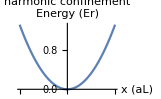

```mathematica
potential[x_,f0x_]:=1/2 massK40 (2π f0x)^2(x λlat/2)^2/Erecoil;
Plot[potential[x,f0],{x,-50,50},PlotLabel->"harmonic confinement",AxesLabel->{"x (aL)","Energy (Er)"}]
```

```mathematica
onsiteU=0.577687 h kHz/Erecoil (174(1-7.5/(20-202.1)))/174 
tunnelling= 0.12642;(*unit is Erecoil*)
(*tempβ=4;*)
(*1/(kB Temp) = 1/Er*)
```

0.133733

```mathematica
0.577687 h kHz/Erecoil(174(1-7.5/(20-202.1)))/174
```

0.133733

## manipulate folder list && calculate(1Er,t=0.178514,U=)

```mathematica
folderls={"20G",         "180G",     "197.5G","200G",     "201G",  "205G",       "206G",          "207G",          "210G",          "222Er",       "333Er",       "444Er",      "3.5Er",       "111Er",  "1Dp21010Er"};
ttls=         {0.12642,     0.12642,  0.12642,   0.12642,   0.12642,0.12642,    0.12642,        0.12642,         0.12642,       0.14305,       0.111252,    0.0856614,  0.0976734,   0.178514,    0.1};
UUls=         {0.0943664,0.121392,0.238406,0.414325, 0.70859,-0.143764, -0.0836618,-0.0480913, 0.00458904, 0.0758841, 0.113742,     0.154097,    0.133733,    0.0426963,    0.1};
```

```mathematica
For[iifolder=15,iifolder≤ 15,iifolder++,
{
pathexp=StringJoin["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/","cubic-results-",folderls⟦iifolder⟧];
ttvalue=ttls⟦iifolder⟧;
UUvalue=UUls⟦iifolder⟧;
Print[StringJoin[ToString[folderls⟦iifolder⟧],"; t=",ToString[ttvalue],";U=",ToString[UUvalue]]];

calcedpath=StringJoin[pathexp,"/yes.txt"];
calcedcheck=Check[Import[calcedpath];True,False];
If[calcedcheck,
{
Print["calculated!"]
},
{
Print["start to calculate!"];
If[Length[StringCases[folderls⟦iifolder⟧,x_~~"G"-> x]]≥ 1,
{
Print["B field data sets"]
},
{
Print["lat depth data sets"];
(*trap freq*);
Vlatx=1;(*ToExpression[StringCases[folderls⟦iifolder⟧,x_~~"Er"-> x]⟦1⟧];*)(*unit: Er*);
Vlaty=Vlatx;
Vlatz=Vlatx;
bandnumber=6;
fx=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π);
fy=√(2/massK40((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π);
fz=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π);
f0= √(1*xdtfreq^2+fx^2);
potential[x_,f0x_]:=1/2 massK40 (2π f0x)^2(x λlat/2)^2/Erecoil;
Print["vlat=",ToString[Vlatx],";    f0=",ToString[f0]];
(*end of trap freq & potential*);
}
];
writegeomfile=0;
If[writegeomfile==1 ,
{ 
(*write geom file*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
tJold=ww⟦35⟧; 
onsiteUold=ww⟦60⟧;
tJnew=ttvalue;
onsiteUnew=UUvalue;
wwtJold1=StringJoin["0 0 1.0 0.0 0.0 ",ToString[tJold]," ",ToString[tJold]," 0.0"];
wwtJold2=StringJoin["0 0 0.0 1.0 0.0 ",ToString[tJold]," ",ToString[tJold]," 0.0"];
wwtJold3=StringJoin["0 0 0.0 0.0 1.0 ",ToString[tJold]," ",ToString[tJold]," 0.0"];
wwUold=     StringJoin["0 0 0.0 0.0 0.0 0.0 0.0 ",ToString[onsiteUold]];

wwtJnew1=StringJoin["0 0 1.0 0.0 0.0 ",ToString[tJnew]," ",ToString[tJnew]," 0.0"];
wwtJnew2=StringJoin["0 0 0.0 1.0 0.0 ",ToString[tJnew]," ",ToString[tJnew]," 0.0"];
wwtJnew3=StringJoin["0 0 0.0 0.0 1.0 ",ToString[tJnew]," ",ToString[tJnew]," 0.0"];
wwUnew=     StringJoin["0 0 0.0 0.0 0.0 0.0 0.0 ",ToString[onsiteUnew]];

writenew=StringReplace[writetemp,{wwtJold1-> wwtJnew1,wwtJold2-> wwtJnew2,wwtJold3-> wwtJnew3,wwUold-> wwUnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom",writenew,"Text"];
(*end of write geom file*);
},
{
(*read geom file*)
(*end of read geom file*)
}]

(*start MC simulation*);

Run["clear"];

iitempstart=0.0222;iitempend=0.15;δiitemp=0.021;
iiμstart=-7.021;iiμend=3.01;δμ=0.0402;
(*save readme files*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
Export[StringJoin[pathexp,"/readme_in"],write,"Text"];

write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom","Text"];
Export[StringJoin[pathexp,"/readme_cubic.geom"],write,"Text"];
paralist={0,0};
paralist⟦1⟧={"iitempstart","iitempend","δiitemp","iiμstart","iiμend","δμ","onsiteU","tunnelling"};
paralist⟦2⟧={iitempstart,iitempend,δiitemp,iiμstart,iiμend,δμ,onsiteUnew,tJnew};
Export[StringJoin[pathexp,"/readme_paralist.txt"],paralist,"TSV"];

(*end save readme files*);
outputstring={"tempβ","μ","density","err","doublon","err"};
calcoutput={outputstring};
For[iitemp=iitempstart,iitemp≤ iitempend,iitemp=iitemp+δiitemp,
{
Print[Now];
iitempβ=1/iitemp;
Ltemp=50;
dtempβ=iitempβ/Ltemp;
(*write the tempβ, into the in file for calculation*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwdτ=ww⟦Position[ww,"dtau"]⟦1,1⟧+1⟧;
wwL=ww⟦Position[ww,"L"]⟦1,1⟧+1⟧;

wwdτold=StringJoin["dtau   =  ",ToString[wwdτ]];
wwLold=  StringJoin["L      =  ",ToString[wwL]];

wwdτnew=StringJoin["dtau   =  ",ToString[dtempβ]];
wwLnew=  StringJoin["L      =  ",ToString[Ltemp]];

writenew=StringReplace[writetemp,{wwLold-> wwLnew,wwdτold-> wwdτnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*end of ..........*)(*write the tempβ, into the in file for calculation*);

For[iiμ=iiμstart,iiμ≤ iiμend,iiμ=iiμ+δμ,
{
If[Abs[iiμ]<0.00001,iiμ=0];
(*write the chemical potential μ into the in file for calculation*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwμup=ww⟦Position[ww,"up"]⟦1,1⟧+1⟧;
wwμdn=ww⟦Position[ww,"dn"]⟦1,1⟧+1⟧;

wwμupold=StringJoin["mu_up  =  ",ToString[wwμup]];
wwμdnold=StringJoin["mu_dn  =  ",ToString[wwμdn]];

wwμupnew=StringJoin["mu_up  =  ",ToString[iiμ]];
wwμdnnew=StringJoin["mu_dn  =  ",ToString[iiμ]];

writenew=StringReplace[writetemp,{wwμupold-> wwμupnew,wwμdnold-> wwμdnnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*write the chemical potential μ into the in file for calculation*);

(*run the program*);
Run["cd ~/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom; ./ggeom in"];
(*end of run the program*);

(*get results*);

out=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/test.out","TSV"];

outddensity=out⟦34,1⟧;
outb=TextCases[outddensity,"Word"];
density11=ToExpression[StringSplit[outb⟦2⟧,"E"]];
densityerr11=ToExpression[StringSplit[outb⟦3⟧,"E"]];
densitytemp=density11⟦1⟧*10^density11⟦2⟧;
densityerrtemp=densityerr11⟦1⟧*10^densityerr11⟦2⟧;

outdoublon=out⟦45,1⟧;
outd=TextCases[outdoublon,"Word"];
doublon11=ToExpression[StringSplit[outd⟦3⟧,"E"]];
doublonerr11=ToExpression[StringSplit[outd⟦4⟧,"E"]];
doublontemp=doublon11⟦1⟧*10^doublon11⟦2⟧;
doublonerrtemp=doublonerr11⟦1⟧*10^doublonerr11⟦2⟧;

Print[StringJoin["tempβ:",ToString[iitempβ],"   ","μ :", ToString[iiμ],"    ","density :" ,ToString[densitytemp], "   ","err:", ToString[densityerrtemp],"     ","doublon:",ToString[doublontemp],"   ","err:",ToString[doublonerrtemp]]];
(*end of (*get results*)*)
(*outputstring={"tempβ","μ","density","err","doublon","err"};*)
outputtemp={iitempβ,iiμ,densitytemp,densityerrtemp,doublontemp,doublonerrtemp};
calcoutput=Join[calcoutput,{outputtemp}];

}
];
Print["END of CALCULATION!"];
}
];
Export[StringJoin[pathexp,"/calcoutput.txt"],calcoutput,"TSV"];
Export[StringJoin[pathexp,"/yes.txt"],1];
(*end of MC simulation*);
Print["End of Exportation!"];
Print["///////////////////////////////////////////////////////////////////////////////////////"];
}];(*end of calcedcheck*);
};
]
```

1Dp21010Er; t=0.1;U=0.1

Import::nffil: File not found during Import.

start to calculate!

lat depth data sets

vlat=1;    f0=44.3855

Sun 8 Oct 2017 00:49:59GMT-4.

tempβ:45.045   μ :-7.021    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.9808    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.9406    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.9004    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.8602    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.82    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.7798    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.7396    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.6994    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.6592    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.619    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.5788    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.5386    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.4984    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.4582    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.418    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.3778    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.3376    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.2974    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.2572    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.217    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.1768    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.1366    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.0964    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.0562    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-6.016    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.9758    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.9356    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.8954    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.8552    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.815    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.7748    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.7346    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.6944    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.6542    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.614    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.5738    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.5336    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.4934    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.4532    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.413    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.3728    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.3326    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.2924    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.2522    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.212    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.1718    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.1316    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.0914    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.0512    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-5.011    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.9708    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.9306    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.8904    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.8502    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.81    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.7698    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.7296    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.6894    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.6492    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.609    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.5688    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.5286    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.4884    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.4482    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.408    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.3678    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.3276    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.2874    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.2472    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.207    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.1668    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.1266    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.0864    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.0462    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-4.006    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.9658    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.9256    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.8854    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.8452    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.805    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.7648    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.7246    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.6844    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.6442    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.604    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.5638    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.5236    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.4834    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.4432    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.403    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.3628    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.3226    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.2824    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.2422    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.202    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.1618    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.1216    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.0814    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.0412    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-3.001    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.9608    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.9206    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.8804    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.8402    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.8    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.7598    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.7196    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.6794    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.6392    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.599    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.5588    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.5186    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.4784    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.4382    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.398    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.3578    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.3176    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.2774    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.2372    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.197    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.1568    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.1166    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.0764    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-2.0362    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.996    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.9558    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.9156    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.8754    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.8352    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.795    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.7548    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.7146    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.6744    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.6342    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.594    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.5538    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.5136    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.4734    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.4332    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.393    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.3528    density :0.   err:0.     doublon:0.   err:0.

tempβ:45.045   μ :-1.3126    density :          -20
3.46945 10   err:          -20
3.46945 10     doublon:0.   err:0.

tempβ:45.045   μ :-1.2724    density :          -18
2.72352 10   err:          -18
1.08805 10     doublon:0.   err:0.

tempβ:45.045   μ :-1.2322    density :          -17
3.71231 10   err:          -18
8.23569 10     doublon:0.   err:0.

tempβ:45.045   μ :-1.192    density :          -16
3.22936 10   err:          -17
5.11888 10     doublon:          -33
2.11275 10   err:          -34
4.07513 10

tempβ:45.045   μ :-1.1518    density :          -15
2.09267 10   err:          -16
3.09156 10     doublon:          -31
2.05678 10   err:          -32
3.26336 10

tempβ:45.045   μ :-1.1116    density :          -14
1.28415 10   err:          -15
1.89306 10     doublon:          -30
8.30083 10   err:          -30
1.31819 10

tempβ:45.045   μ :-1.0714    density :          -14
7.85664 10   err:          -14
1.15744 10     doublon:          -28
3.12619 10   err:          -29
4.95368 10

tempβ:45.045   μ :-1.0312    density :          -13
4.80478 10   err:          -14
7.07842 10     doublon:          -26
1.16968 10   err:          -27
1.85369 10

tempβ:45.045   μ :-0.991    density :          -12
2.93832 10   err:          -13
4.32876 10     doublon:         -25
4.3743 10   err:          -26
6.93103 10

tempβ:45.045   μ :-0.9508    density :         -11
1.7969 10   err:          -12
2.64721 10     doublon:          -23
1.63593 10   err:          -24
2.59213 10

tempβ:45.045   μ :-0.9106    density :          -10
1.09888 10   err:          -11
1.61888 10     doublon:          -22
6.11806 10   err:          -23
9.69403 10

tempβ:45.045   μ :-0.8704    density :          -10
6.72009 10   err:          -11
9.90008 10     doublon:          -20
2.28804 10   err:          -21
3.62539 10

tempβ:45.045   μ :-0.8302    density :          -9
4.10961 10   err:         -10
6.0543 10     doublon:          -19
8.55686 10   err:          -19
1.35583 10

tempβ:45.045   μ :-0.79    density :          -8
2.51319 10   err:          -9
3.70244 10     doublon:          -17
3.20011 10   err:          -18
5.07055 10

tempβ:45.045   μ :-0.7498    density :          -7
1.53691 10   err:          -8
2.26418 10     doublon:          -15
1.19678 10   err:          -16
1.89627 10

tempβ:45.045   μ :-0.7096    density :          -7
9.39865 10   err:          -7
1.38457 10     doublon:          -14
4.47558 10   err:          -15
7.09123 10

tempβ:45.045   μ :-0.6694    density :          -6
5.74944 10   err:          -7
8.38871 10     doublon:          -12
1.68992 10   err:          -13
2.63133 10

tempβ:45.045   μ :-0.6292    density :0.0000355335   err:          -6
5.31823 10     doublon:          -11
6.70095 10   err:          -11
1.11995 10

tempβ:45.045   μ :-0.589    density :0.000189071   err:0.0000228872     doublon:          -9
2.13254 10   err:          -10
2.96585 10

tempβ:45.045   μ :-0.5488    density :0.00126417   err:0.0000910762     doublon:          -8
7.28312 10   err:          -9
6.27362 10

tempβ:45.045   μ :-0.5086    density :0.00672195   err:0.00118266     doublon:          -6
2.49672 10   err:          -7
4.87678 10

tempβ:45.045   μ :-0.4684    density :0.0283947   err:0.00260747     doublon:0.0000416078   err:          -6
2.43515 10

tempβ:45.045   μ :-0.4282    density :0.0849324   err:0.00324502     doublon:0.000466517   err:0.000034947

tempβ:45.045   μ :-0.388    density :0.176119   err:0.00287638     doublon:0.00271445   err:0.000140375

tempβ:45.045   μ :-0.3478    density :0.270747   err:0.00378443     doublon:0.00799748   err:0.000317657

tempβ:45.045   μ :-0.3076    density :0.372575   err:0.0040681     doublon:0.0179439   err:0.000543573

tempβ:45.045   μ :-0.2674    density :0.44649   err:0.00328718     doublon:0.0264213   err:0.000645899

tempβ:45.045   μ :-0.2272    density :0.490889   err:0.00117591     doublon:0.0318806   err:0.000284071

tempβ:45.045   μ :-0.187    density :0.523335   err:0.00528803     doublon:0.0374746   err:0.000883187

tempβ:45.045   μ :-0.1468    density :0.571929   err:0.00312184     doublon:0.0454373   err:0.000632298

tempβ:45.045   μ :-0.1066    density :0.690758   err:0.00441991     doublon:0.0668246   err:0.00120792

tempβ:45.045   μ :-0.0664    density :0.850951   err:0.00525079     doublon:0.101378   err:0.000799653

tempβ:45.045   μ :-0.0262    density :0.955787   err:0.00471635     doublon:0.126888   err:0.00147184

tempβ:45.045   μ :0.014    density :1.02183   err:0.00120196     doublon:0.161128   err:0.00269424

tempβ:45.045   μ :0.0542    density :1.10666   err:0.011856     doublon:0.221975   err:0.00982923

tempβ:45.045   μ :0.0944    density :1.26551   err:0.00926886     doublon:0.342473   err:0.00797221

tempβ:45.045   μ :0.1346    density :1.37896   err:0.00304331     doublon:0.433176   err:0.00277967

tempβ:45.045   μ :0.1748    density :1.47077   err:0.00396889     doublon:0.508325   err:0.00338073

tempβ:45.045   μ :0.215    density :1.50255   err:0.00179237     doublon:0.534645   err:0.00190319

tempβ:45.045   μ :0.2552    density :1.53513   err:0.00345953     doublon:0.563805   err:0.00315653

tempβ:45.045   μ :0.2954    density :1.60602   err:0.00248886     doublon:0.626049   err:0.00213523

tempβ:45.045   μ :0.3356    density :1.69961   err:0.00195367     doublon:0.709888   err:0.00150615

tempβ:45.045   μ :0.3758    density :1.80336   err:0.00293189     doublon:0.806622   err:0.00269336

tempβ:45.045   μ :0.416    density :1.88917   err:0.00608448     doublon:0.889959   err:0.00604714

tempβ:45.045   μ :0.4562    density :1.9623   err:0.00195027     doublon:0.962394   err:0.00194696

tempβ:45.045   μ :0.4964    density :1.9897   err:0.00167603     doublon:0.989703   err:0.00167485

tempβ:45.045   μ :0.5366    density :1.99841   err:0.0000705101     doublon:0.998412   err:0.0000705089

tempβ:45.045   μ :0.5768    density :1.99965   err:0.0000360005     doublon:0.999647   err:0.000036

tempβ:45.045   μ :0.617    density :1.99994   err:          -6
9.57664 10     doublon:0.999939   err:         -6
9.5766 10

tempβ:45.045   μ :0.6572    density :1.99999   err:          -6
1.45077 10     doublon:0.99999   err:          -6
1.45076 10

tempβ:45.045   μ :0.6974    density :2.   err:          -7
2.37892 10     doublon:0.999998   err:          -7
2.37892 10

tempβ:45.045   μ :0.7376    density :2.   err:         -8
3.9226 10     doublon:1.   err:         -8
3.9226 10

tempβ:45.045   μ :0.7778    density :2.   err:          -9
6.41438 10     doublon:1.   err:          -9
6.41438 10

tempβ:45.045   μ :0.818    density :2.   err:          -9
1.04889 10     doublon:1.   err:          -9
1.04889 10

tempβ:45.045   μ :0.8582    density :2.   err:          -10
1.71516 10     doublon:1.   err:          -10
1.71516 10

tempβ:45.045   μ :0.8984    density :2.   err:          -11
2.80467 10     doublon:1.   err:          -11
2.80466 10

tempβ:45.045   μ :0.9386    density :2.   err:          -12
4.58615 10     doublon:1.   err:          -12
4.58611 10

tempβ:45.045   μ :0.9788    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.019    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.0592    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.0994    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.1396    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.1798    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.22    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.2602    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.3004    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.3406    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.3808    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.421    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.4612    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.5014    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.5416    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.5818    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.622    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.6622    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.7024    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.7426    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.7828    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.823    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.8632    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.9034    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.9436    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :1.9838    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.024    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.0642    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.1044    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.1446    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.1848    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.225    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.2652    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.3054    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.3456    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.3858    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.426    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.4662    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.5064    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.5466    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.5868    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.627    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.6672    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.7074    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.7476    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.7878    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.828    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.8682    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.9084    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.9486    density :2.   err:0.     doublon:1.   err:0.

tempβ:45.045   μ :2.9888    density :2.   err:0.     doublon:1.   err:0.

END of CALCULATION!

Sun 8 Oct 2017 02:15:29GMT-4.

tempβ:23.1481   μ :-7.021    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.9808    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.9406    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.9004    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.8602    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.82    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.7798    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.7396    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.6994    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.6592    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.619    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.5788    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.5386    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.4984    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.4582    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.418    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.3778    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.3376    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.2974    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.2572    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.217    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.1768    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.1366    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.0964    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.0562    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-6.016    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.9758    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.9356    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.8954    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.8552    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.815    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.7748    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.7346    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.6944    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.6542    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.614    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.5738    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.5336    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.4934    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.4532    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.413    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.3728    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.3326    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.2924    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.2522    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.212    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.1718    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.1316    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.0914    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.0512    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-5.011    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.9708    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.9306    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.8904    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.8502    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.81    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.7698    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.7296    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.6894    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.6492    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.609    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.5688    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.5286    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.4884    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.4482    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.408    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.3678    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.3276    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.2874    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.2472    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.207    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.1668    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.1266    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.0864    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.0462    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-4.006    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.9658    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.9256    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.8854    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.8452    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.805    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.7648    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.7246    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.6844    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.6442    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.604    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.5638    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.5236    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.4834    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.4432    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.403    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.3628    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.3226    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.2824    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.2422    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.202    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.1618    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.1216    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.0814    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.0412    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-3.001    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.9608    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.9206    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.8804    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.8402    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.8    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.7598    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.7196    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.6794    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.6392    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.599    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.5588    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.5186    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.4784    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.4382    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.398    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.3578    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.3176    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.2774    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.2372    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.197    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.1568    density :0.   err:0.     doublon:0.   err:0.

tempβ:23.1481   μ :-2.1166    density :          -19
2.25514 10   err:          -19
1.11752 10     doublon:0.   err:0.

tempβ:23.1481   μ :-2.0764    density :          -18
1.82146 10   err:          -19
4.59784 10     doublon:0.   err:0.

tempβ:23.1481   μ :-2.0362    density :          -18
8.69096 10   err:         -18
2.0076 10     doublon:0.   err:0.

tempβ:23.1481   μ :-1.996    density :          -17
3.43649 10   err:          -18
5.34814 10     doublon:0.   err:0.

tempβ:23.1481   μ :-1.9558    density :          -16
1.14648 10   err:         -17
1.3931 10     doublon:          -34
1.11704 10   err:          -35
5.00927 10

tempβ:23.1481   μ :-1.9156    density :          -16
3.28557 10   err:          -17
3.41472 10     doublon:          -33
2.31882 10   err:          -34
3.16351 10

tempβ:23.1481   μ :-1.8754    density :          -16
8.71213 10   err:          -17
8.33945 10     doublon:          -32
3.12906 10   err:          -33
2.28569 10

tempβ:23.1481   μ :-1.8352    density :          -15
2.22499 10   err:          -16
2.11623 10     doublon:          -31
2.50469 10   err:        -32
1.291 10

tempβ:23.1481   μ :-1.795    density :          -15
5.65074 10   err:         -16
5.3835 10     doublon:          -30
1.70597 10   err:          -32
9.90346 10

tempβ:23.1481   μ :-1.7548    density :          -14
1.43401 10   err:         -15
1.3667 10     doublon:          -29
1.10553 10   err:          -31
6.96466 10

tempβ:23.1481   μ :-1.7146    density :          -14
3.63759 10   err:          -15
3.46711 10     doublon:          -29
7.12541 10   err:          -30
4.45166 10

tempβ:23.1481   μ :-1.6744    density :          -14
9.22555 10   err:          -15
8.79177 10     doublon:          -28
4.58932 10   err:          -29
2.85074 10

tempβ:23.1481   μ :-1.6342    density :          -13
2.33956 10   err:          -14
2.22922 10     doublon:          -27
2.95249 10   err:          -28
1.83458 10

tempβ:23.1481   μ :-1.594    density :          -13
5.93294 10   err:          -14
5.65305 10     doublon:          -26
1.89863 10   err:          -27
1.18049 10

tempβ:23.1481   μ :-1.5538    density :          -12
1.50455 10   err:          -13
1.43357 10     doublon:          -25
1.22103 10   err:          -27
7.58927 10

tempβ:23.1481   μ :-1.5136    density :          -12
3.81542 10   err:          -13
3.63542 10     doublon:          -25
7.85247 10   err:          -26
4.88129 10

tempβ:23.1481   μ :-1.4734    density :          -12
9.67559 10   err:         -13
9.2191 10     doublon:          -24
5.04987 10   err:          -25
3.13912 10

tempβ:23.1481   μ :-1.4332    density :          -11
2.45365 10   err:          -12
2.33789 10     doublon:          -23
3.24751 10   err:          -24
2.01877 10

tempβ:23.1481   μ :-1.393    density :          -11
6.22225 10   err:         -12
5.9287 10     doublon:          -22
2.08843 10   err:          -23
1.29824 10

tempβ:23.1481   μ :-1.3528    density :          -10
1.57791 10   err:          -11
1.50347 10     doublon:          -21
1.34305 10   err:          -23
8.34881 10

tempβ:23.1481   μ :-1.3126    density :          -10
4.00146 10   err:          -11
3.81267 10     doublon:          -21
8.63697 10   err:          -22
5.36903 10

tempβ:23.1481   μ :-1.2724    density :          -9
1.01474 10   err:          -11
9.66862 10     doublon:          -20
5.55433 10   err:          -21
3.45276 10

tempβ:23.1481   μ :-1.2322    density :          -9
2.57329 10   err:          -10
2.45188 10     doublon:          -19
3.57192 10   err:          -20
2.22043 10

tempβ:23.1481   μ :-1.192    density :          -9
6.52565 10   err:          -10
6.21777 10     doublon:          -18
2.29706 10   err:          -19
1.42793 10

tempβ:23.1481   μ :-1.1518    density :          -8
1.65485 10   err:          -9
1.57678 10     doublon:          -17
1.47721 10   err:          -19
9.18283 10

tempβ:23.1481   μ :-1.1116    density :          -8
4.19656 10   err:          -9
3.99857 10     doublon:          -17
9.49977 10   err:          -18
5.90536 10

tempβ:23.1481   μ :-1.0714    density :          -7
1.06421 10   err:        -8
1.014 10     doublon:          -16
6.10918 10   err:          -17
3.79766 10

tempβ:23.1481   μ :-1.0312    density :          -7
2.69875 10   err:          -8
2.57142 10     doublon:          -15
3.92873 10   err:          -16
2.44221 10

tempβ:23.1481   μ :-0.991    density :          -7
6.84378 10   err:          -8
6.52083 10     doublon:         -14
2.5265 10   err:          -15
1.57053 10

tempβ:23.1481   μ :-0.9508    density :          -6
1.73265 10   err:          -7
1.64015 10     doublon:          -13
1.62222 10   err:          -14
1.00949 10

tempβ:23.1481   μ :-0.9106    density :          -6
4.39372 10   err:          -7
4.15897 10     doublon:          -12
1.04318 10   err:          -14
6.49131 10

tempβ:23.1481   μ :-0.8704    density :0.0000110725   err:          -6
1.05148 10     doublon:          -12
6.70211 10   err:          -13
4.31302 10

tempβ:23.1481   μ :-0.8302    density :0.0000292209   err:          -6
2.88704 10     doublon:         -11
4.5576 10   err:          -12
3.81433 10

tempβ:23.1481   μ :-0.79    density :0.000071726   err:          -6
7.44608 10     doublon:          -10
2.82993 10   err:        -11
2.083 10

tempβ:23.1481   μ :-0.7498    density :0.000170145   err:0.0000141345     doublon:          -9
1.69814 10   err:          -11
8.63128 10

tempβ:23.1481   μ :-0.7096    density :0.000441097   err:0.0000260951     doublon:          -8
1.14517 10   err:          -10
7.89406 10

tempβ:23.1481   μ :-0.6694    density :0.00101285   err:0.0000427092     doublon:          -8
5.88159 10   err:          -9
2.65994 10

tempβ:23.1481   μ :-0.6292    density :0.00286248   err:0.000132113     doublon:          -7
3.76792 10   err:          -8
2.82303 10

tempβ:23.1481   μ :-0.589    density :0.00603727   err:0.000936405     doublon:          -6
2.02217 10   err:          -7
1.47559 10

tempβ:23.1481   μ :-0.5488    density :0.0142157   err:0.000655209     doublon:0.0000142537   err:          -6
1.60756 10

tempβ:23.1481   μ :-0.5086    density :0.0300327   err:0.00139959     doublon:0.0000716565   err:          -6
6.22253 10

tempβ:23.1481   μ :-0.4684    density :0.0658507   err:0.00415642     doublon:0.000311082   err:0.0000190651

tempβ:23.1481   μ :-0.4282    density :0.12094   err:0.000872592     doublon:0.00119241   err:0.0000579687

tempβ:23.1481   μ :-0.388    density :0.193286   err:0.0010465     doublon:0.00352599   err:0.0000962218

tempβ:23.1481   μ :-0.3478    density :0.27381   err:0.00412014     doublon:0.00832513   err:0.000224207

tempβ:23.1481   μ :-0.3076    density :0.347873   err:0.00619733     doublon:0.0155337   err:0.000512961

tempβ:23.1481   μ :-0.2674    density :0.422402   err:0.00486801     doublon:0.023119   err:0.000594176

tempβ:23.1481   μ :-0.2272    density :0.485142   err:0.00279359     doublon:0.0315327   err:0.000460707

tempβ:23.1481   μ :-0.187    density :0.557844   err:0.00436628     doublon:0.0426674   err:0.000655985

tempβ:23.1481   μ :-0.1468    density :0.647718   err:0.00530451     doublon:0.0566196   err:0.00127778

tempβ:23.1481   μ :-0.1066    density :0.748839   err:0.0112809     doublon:0.0778872   err:0.00106501

tempβ:23.1481   μ :-0.0664    density :0.853908   err:0.00597782     doublon:0.103422   err:0.00153557

tempβ:23.1481   μ :-0.0262    density :0.945122   err:0.00181929     doublon:0.13622   err:0.00196882

tempβ:23.1481   μ :0.014    density :1.02989   err:0.00117104     doublon:0.174691   err:0.00334165

tempβ:23.1481   μ :0.0542    density :1.11025   err:0.0062217     doublon:0.223113   err:0.00761588

tempβ:23.1481   μ :0.0944    density :1.21512   err:0.00426787     doublon:0.299913   err:0.00452852

tempβ:23.1481   μ :0.1346    density :1.32718   err:0.00720546     doublon:0.390091   err:0.00693406

tempβ:23.1481   μ :0.1748    density :1.41069   err:0.00786071     doublon:0.456424   err:0.00702432

tempβ:23.1481   μ :0.215    density :1.48879   err:0.00411985     doublon:0.522969   err:0.00418988

tempβ:23.1481   μ :0.2552    density :1.55473   err:0.00464766     doublon:0.580163   err:0.0044102

tempβ:23.1481   μ :0.2954    density :1.63593   err:0.00144885     doublon:0.652591   err:0.00145183

tempβ:23.1481   μ :0.3356    density :1.69921   err:0.00629323     doublon:0.709316   err:0.00587935

tempβ:23.1481   μ :0.3758    density :1.77578   err:0.00413814     doublon:0.780864   err:0.00392018

tempβ:23.1481   μ :0.416    density :1.85519   err:0.0014564     doublon:0.85696   err:0.00146805

tempβ:23.1481   μ :0.4562    density :1.91854   err:0.00242809     doublon:0.919033   err:0.00239156

tempβ:23.1481   μ :0.4964    density :1.96229   err:0.0022265     doublon:0.962392   err:0.00221917

tempβ:23.1481   μ :0.5366    density :1.98069   err:0.00173238     doublon:0.980715   err:0.00173064

tempβ:23.1481   μ :0.5768    density :1.99192   err:0.000568567     doublon:0.991922   err:0.000568388

tempβ:23.1481   μ :0.617    density :1.99642   err:0.000216533     doublon:0.996423   err:0.000216496

tempβ:23.1481   μ :0.6572    density :1.99867   err:0.0000581365     doublon:0.99867   err:0.0000581301

tempβ:23.1481   μ :0.6974    density :1.99944   err:0.0000249308     doublon:0.999444   err:0.0000249301

tempβ:23.1481   μ :0.7376    density :1.99976   err:0.0000219835     doublon:0.999756   err:0.0000219832

tempβ:23.1481   μ :0.7778    density :1.9999   err:0.0000102367     doublon:0.999904   err:0.0000102367

tempβ:23.1481   μ :0.818    density :1.99996   err:          -6
3.77002 10     doublon:0.999962   err:          -6
3.77002 10

tempβ:23.1481   μ :0.8582    density :1.99999   err:          -6
1.41773 10     doublon:0.999985   err:          -6
1.41773 10

tempβ:23.1481   μ :0.8984    density :1.99999   err:         -7
5.5159 10     doublon:0.999994   err:          -7
5.51589 10

tempβ:23.1481   μ :0.9386    density :2.   err:          -7
2.17532 10     doublon:0.999998   err:          -7
2.17532 10

tempβ:23.1481   μ :0.9788    density :2.   err:          -8
8.64864 10     doublon:0.999999   err:          -8
8.64864 10

tempβ:23.1481   μ :1.019    density :2.   err:          -8
3.41051 10     doublon:1.   err:          -8
3.41051 10

tempβ:23.1481   μ :1.0592    density :2.   err:          -8
1.34489 10     doublon:1.   err:          -8
1.34489 10

tempβ:23.1481   μ :1.0994    density :2.   err:          -9
5.30338 10     doublon:1.   err:          -9
5.30338 10

tempβ:23.1481   μ :1.1396    density :2.   err:          -9
2.09131 10     doublon:1.   err:          -9
2.09131 10

tempβ:23.1481   μ :1.1798    density :2.   err:          -10
8.24675 10     doublon:1.   err:          -10
8.24675 10

tempβ:23.1481   μ :1.22    density :2.   err:          -10
3.25198 10     doublon:1.   err:          -10
3.25198 10

tempβ:23.1481   μ :1.2602    density :2.   err:          -10
1.28237 10     doublon:1.   err:          -10
1.28237 10

tempβ:23.1481   μ :1.3004    density :2.   err:          -11
5.05682 10     doublon:1.   err:          -11
5.05682 10

tempβ:23.1481   μ :1.3406    density :2.   err:         -11
1.9941 10     doublon:1.   err:          -11
1.99408 10

tempβ:23.1481   μ :1.3808    density :2.   err:         -12
7.8634 10     doublon:1.   err:          -12
7.86331 10

tempβ:23.1481   μ :1.421    density :2.   err:          -12
3.10072 10     doublon:1.   err:          -12
3.10083 10

tempβ:23.1481   μ :1.4612    density :2.   err:0.     doublon:1.   err:          -12
1.22275 10

tempβ:23.1481   μ :1.5014    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.5416    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.5818    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.622    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.6622    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.7024    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.7426    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.7828    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.823    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.8632    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.9034    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.9436    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :1.9838    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.024    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.0642    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.1044    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.1446    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.1848    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.225    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.2652    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.3054    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.3456    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.3858    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.426    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.4662    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.5064    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.5466    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.5868    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.627    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.6672    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.7074    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.7476    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.7878    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.828    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.8682    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.9084    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.9486    density :2.   err:0.     doublon:1.   err:0.

tempβ:23.1481   μ :2.9888    density :2.   err:0.     doublon:1.   err:0.

END of CALCULATION!

Sun 8 Oct 2017 03:41:42GMT-4.

tempβ:15.5763   μ :-7.021    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.9808    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.9406    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.9004    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.8602    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.82    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.7798    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.7396    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.6994    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.6592    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.619    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.5788    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.5386    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.4984    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.4582    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.418    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.3778    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.3376    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.2974    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.2572    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.217    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.1768    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.1366    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.0964    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.0562    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-6.016    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.9758    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.9356    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.8954    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.8552    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.815    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.7748    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.7346    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.6944    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.6542    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.614    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.5738    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.5336    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.4934    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.4532    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.413    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.3728    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.3326    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.2924    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.2522    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.212    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.1718    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.1316    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.0914    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.0512    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-5.011    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.9708    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.9306    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.8904    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.8502    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.81    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.7698    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.7296    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.6894    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.6492    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.609    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.5688    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.5286    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.4884    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.4482    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.408    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.3678    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.3276    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.2874    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.2472    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.207    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.1668    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.1266    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.0864    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.0462    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-4.006    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.9658    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.9256    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.8854    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.8452    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.805    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.7648    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.7246    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.6844    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.6442    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.604    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.5638    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.5236    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.4834    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.4432    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.403    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.3628    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.3226    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.2824    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.2422    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.202    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.1618    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.1216    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.0814    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.0412    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-3.001    density :0.   err:0.     doublon:0.   err:0.

tempβ:15.5763   μ :-2.9608    density :          -20
6.93889 10   err:          -20
6.93889 10     doublon:0.   err:0.

tempβ:15.5763   μ :-2.9206    density :          -19
5.20417 10   err:          -19
1.45137 10     doublon:0.   err:0.

tempβ:15.5763   μ :-2.8804    density :          -18
1.56125 10   err:          -19
3.86925 10     doublon:0.   err:0.

tempβ:15.5763   μ :-2.8402    density :         -18
5.6205 10   err:          -18
1.15441 10     doublon:0.   err:0.

tempβ:15.5763   μ :-2.8    density :          -17
1.57339 10   err:         -18
4.3173 10     doublon:0.   err:0.

tempβ:15.5763   μ :-2.7598    density :          -17
3.81639 10   err:          -18
5.09718 10     doublon:          -36
5.77779 10   err:          -36
3.85186 10

tempβ:15.5763   μ :-2.7196    density :          -17
9.01883 10   err:          -18
9.05591 10     doublon:         -35
5.5852 10   err:          -35
1.98287 10

tempβ:15.5763   μ :-2.6794    density :          -16
1.90542 10   err:         -17
1.6321 10     doublon:          -34
5.46964 10   err:          -34
1.13589 10

tempβ:15.5763   μ :-2.6392    density :          -16
3.81639 10   err:          -17
2.94389 10     doublon:          -33
4.53171 10   err:          -34
4.39059 10

tempβ:15.5763   μ :-2.599    density :          -16
7.31516 10   err:          -17
5.31795 10     doublon:          -32
2.46326 10   err:          -33
1.81294 10

tempβ:15.5763   μ :-2.5588    density :          -15
1.38127 10   err:          -16
1.00193 10     doublon:          -31
1.05947 10   err:          -33
7.34581 10

tempβ:15.5763   μ :-2.5186    density :          -15
2.58736 10   err:          -16
1.89755 10     doublon:          -31
3.96901 10   err:          -32
2.30549 10

tempβ:15.5763   μ :-2.4784    density :          -15
4.84149 10   err:          -16
3.53928 10     doublon:          -30
1.42567 10   err:          -32
8.05937 10

tempβ:15.5763   μ :-2.4382    density :          -15
9.05704 10   err:          -16
6.62913 10     doublon:          -30
4.98914 10   err:         -31
2.8224 10

tempβ:15.5763   μ :-2.398    density :          -14
1.69431 10   err:          -15
1.24007 10     doublon:          -29
1.74306 10   err:          -31
9.80578 10

tempβ:15.5763   μ :-2.3578    density :          -14
3.16994 10   err:         -15
2.3191 10     doublon:          -29
6.10739 10   err:          -30
3.46241 10

tempβ:15.5763   μ :-2.3176    density :          -14
5.93013 10   err:          -15
4.33791 10     doublon:          -28
2.13935 10   err:          -29
1.20877 10

tempβ:15.5763   μ :-2.2774    density :          -13
1.10926 10   err:          -15
8.11237 10     doublon:          -28
7.48878 10   err:          -29
4.21733 10

tempβ:15.5763   μ :-2.2372    density :          -13
2.07482 10   err:          -14
1.51744 10     doublon:          -27
2.62135 10   err:          -28
1.47433 10

tempβ:15.5763   μ :-2.197    density :          -13
3.88081 10   err:          -14
2.83831 10     doublon:          -27
9.17059 10   err:          -28
5.16007 10

tempβ:15.5763   μ :-2.1568    density :          -13
7.25876 10   err:          -14
5.30876 10     doublon:          -26
3.20831 10   err:          -27
1.80449 10

tempβ:15.5763   μ :-2.1166    density :         -12
1.3577 10   err:          -14
9.92969 10     doublon:          -25
1.12246 10   err:          -27
6.31569 10

tempβ:15.5763   μ :-2.0764    density :          -12
2.53949 10   err:          -13
1.85729 10     doublon:          -25
3.92687 10   err:          -26
2.20916 10

tempβ:15.5763   μ :-2.0362    density :          -12
4.74993 10   err:          -13
3.47391 10     doublon:          -24
1.37383 10   err:         -26
7.7295 10

tempβ:15.5763   μ :-1.996    density :         -12
8.8844 10   err:          -13
6.49771 10     doublon:          -24
4.80634 10   err:         -25
2.7042 10

tempβ:15.5763   μ :-1.9558    density :          -11
1.66176 10   err:          -12
1.21535 10     doublon:         -23
1.6815 10   err:          -25
9.46075 10

tempβ:15.5763   μ :-1.9156    density :          -11
3.10821 10   err:          -12
2.27322 10     doublon:          -23
5.88273 10   err:          -24
3.30982 10

tempβ:15.5763   μ :-1.8754    density :          -11
5.81368 10   err:         -12
4.2519 10     doublon:          -22
2.05807 10   err:          -23
1.15795 10

tempβ:15.5763   μ :-1.8352    density :          -10
1.08741 10   err:          -12
7.95288 10     doublon:          -22
7.20017 10   err:          -23
4.05108 10

tempβ:15.5763   μ :-1.795    density :          -10
2.03392 10   err:          -11
1.48753 10     doublon:          -21
2.51898 10   err:          -22
1.41727 10

tempβ:15.5763   μ :-1.7548    density :         -10
3.8043 10   err:          -11
2.78231 10     doublon:          -21
8.81266 10   err:          -22
4.95832 10

tempβ:15.5763   μ :-1.7146    density :          -10
7.11566 10   err:          -11
5.20412 10     doublon:          -20
3.08311 10   err:          -21
1.73467 10

tempβ:15.5763   μ :-1.6744    density :          -9
1.33093 10   err:          -11
9.73393 10     doublon:          -19
1.07863 10   err:          -21
6.06873 10

tempβ:15.5763   μ :-1.6342    density :          -9
2.48941 10   err:          -10
1.82066 10     doublon:          -19
3.77357 10   err:          -20
2.12315 10

tempβ:15.5763   μ :-1.594    density :          -9
4.65627 10   err:          -10
3.40542 10     doublon:          -18
1.32019 10   err:          -20
7.42783 10

tempβ:15.5763   μ :-1.5538    density :          -9
8.70922 10   err:          -10
6.36959 10     doublon:          -18
4.61867 10   err:          -19
2.59863 10

tempβ:15.5763   μ :-1.5136    density :        -8
1.629 10   err:          -9
1.19138 10     doublon:          -17
1.61584 10   err:         -19
9.0913 10

tempβ:15.5763   μ :-1.4734    density :          -8
3.04692 10   err:         -9
2.2284 10     doublon:          -17
5.65302 10   err:          -18
3.18059 10

tempβ:15.5763   μ :-1.4332    density :          -8
5.69904 10   err:          -9
4.16806 10     doublon:          -16
1.97771 10   err:          -17
1.11273 10

tempβ:15.5763   μ :-1.393    density :          -7
1.06596 10   err:          -9
7.79605 10     doublon:          -16
6.91901 10   err:          -17
3.89288 10

tempβ:15.5763   μ :-1.3528    density :          -7
1.99381 10   err:          -8
1.45819 10     doublon:          -15
2.42062 10   err:          -16
1.36192 10

tempβ:15.5763   μ :-1.3126    density :          -7
3.72927 10   err:          -8
2.72744 10     doublon:          -15
8.46851 10   err:          -16
4.76467 10

tempβ:15.5763   μ :-1.2724    density :          -7
6.97531 10   err:          -8
5.10145 10     doublon:         -14
2.9627 10   err:          -15
1.66691 10

tempβ:15.5763   μ :-1.2322    density :          -6
1.30278 10   err:          -8
9.44796 10     doublon:          -13
1.03511 10   err:          -15
5.84906 10

tempβ:15.5763   μ :-1.192    density :          -6
2.43673 10   err:          -7
1.76714 10     doublon:         -13
3.6213 10   err:          -14
2.04625 10

tempβ:15.5763   μ :-1.1518    density :          -6
4.55765 10   err:         -7
3.3052 10     doublon:          -12
1.26688 10   err:          -14
7.15857 10

tempβ:15.5763   μ :-1.1116    density :          -6
8.48427 10   err:          -7
6.18077 10     doublon:          -12
4.43441 10   err:          -13
2.54868 10

tempβ:15.5763   μ :-1.0714    density :0.0000158734   err:          -6
1.20953 10     doublon:          -11
1.55257 10   err:          -13
8.82143 10

tempβ:15.5763   μ :-1.0312    density :0.0000297654   err:          -6
2.17708 10     doublon:          -11
5.42157 10   err:          -12
2.87806 10

tempβ:15.5763   μ :-0.991    density :0.0000553285   err:          -6
4.01548 10     doublon:          -10
1.89831 10   err:          -12
9.37822 10

tempβ:15.5763   μ :-0.9508    density :0.000101507   err:          -6
7.33269 10     doublon:          -10
6.45479 10   err:          -11
2.44922 10

tempβ:15.5763   μ :-0.9106    density :0.000196144   err:0.0000120296     doublon:          -9
2.33763 10   err:          -11
9.32328 10

tempβ:15.5763   μ :-0.8704    density :0.000382907   err:0.0000279889     doublon:          -9
8.69068 10   err:          -10
4.30754 10

tempβ:15.5763   μ :-0.8302    density :0.00065149   err:0.0000237819     doublon:          -8
2.74049 10   err:          -9
1.25075 10

tempβ:15.5763   μ :-0.79    density :0.00119166   err:0.0000594381     doublon:          -8
8.87343 10   err:          -9
2.38986 10

tempβ:15.5763   μ :-0.7498    density :0.00239026   err:0.000213101     doublon:          -7
3.09912 10   err:          -8
3.07247 10

tempβ:15.5763   μ :-0.7096    density :0.00368873   err:0.000348469     doublon:          -7
9.20115 10   err:          -8
7.74517 10

tempβ:15.5763   μ :-0.6694    density :0.00649049   err:0.000493849     doublon:          -6
3.40379 10   err:          -7
3.71588 10

tempβ:15.5763   μ :-0.6292    density :0.0125685   err:0.000609989     doublon:0.0000109244   err:          -7
6.95481 10

tempβ:15.5763   μ :-0.589    density :0.022099   err:0.00112387     doublon:0.0000362237   err:          -6
1.74505 10

tempβ:15.5763   μ :-0.5488    density :0.0383742   err:0.00229734     doublon:0.000104484   err:          -6
4.61641 10

tempβ:15.5763   μ :-0.5086    density :0.0696877   err:0.00196267     doublon:0.000353787   err:0.0000207856

tempβ:15.5763   μ :-0.4684    density :0.105038   err:0.00257662     doublon:0.00095931   err:0.0000391849

tempβ:15.5763   μ :-0.4282    density :0.156414   err:0.0049084     doublon:0.00228071   err:0.000080869

tempβ:15.5763   μ :-0.388    density :0.217496   err:0.004565     doublon:0.00466564   err:0.000146185

tempβ:15.5763   μ :-0.3478    density :0.283459   err:0.0058382     doublon:0.00872724   err:0.00036946

tempβ:15.5763   μ :-0.3076    density :0.357012   err:0.00296721     doublon:0.0149878   err:0.00034561

tempβ:15.5763   μ :-0.2674    density :0.434452   err:0.00607752     doublon:0.0220061   err:0.000503133

tempβ:15.5763   μ :-0.2272    density :0.512791   err:0.00414023     doublon:0.0322451   err:0.000589438

tempβ:15.5763   μ :-0.187    density :0.592545   err:0.00398466     doublon:0.0448601   err:0.000711882

tempβ:15.5763   μ :-0.1468    density :0.680652   err:0.00467768     doublon:0.0593695   err:0.000384874

tempβ:15.5763   μ :-0.1066    density :0.780313   err:0.00227493     doublon:0.0817878   err:0.000338553

tempβ:15.5763   μ :-0.0664    density :0.861047   err:0.00460646     doublon:0.108769   err:0.00185133

tempβ:15.5763   μ :-0.0262    density :0.944262   err:0.000979741     doublon:0.139919   err:0.000828792

tempβ:15.5763   μ :0.014    density :1.02892   err:0.000864937     doublon:0.176121   err:0.00264493

tempβ:15.5763   μ :0.0542    density :1.11567   err:0.00305245     doublon:0.235632   err:0.00302288

tempβ:15.5763   μ :0.0944    density :1.20606   err:0.00404314     doublon:0.296018   err:0.00569146

tempβ:15.5763   μ :0.1346    density :1.29829   err:0.00229817     doublon:0.36631   err:0.00217813

tempβ:15.5763   μ :0.1748    density :1.38762   err:0.00410293     doublon:0.4387   err:0.00382821

tempβ:15.5763   μ :0.215    density :1.46968   err:0.00496819     doublon:0.505578   err:0.00574089

tempβ:15.5763   μ :0.2552    density :1.54742   err:0.00316215     doublon:0.572833   err:0.00343513

tempβ:15.5763   μ :0.2954    density :1.6194   err:0.00147303     doublon:0.636474   err:0.00111014

tempβ:15.5763   μ :0.3356    density :1.68913   err:0.00514751     doublon:0.699706   err:0.00510149

tempβ:15.5763   μ :0.3758    density :1.75989   err:0.00218215     doublon:0.765878   err:0.00204375

tempβ:15.5763   μ :0.416    density :1.82204   err:0.00198952     doublon:0.825035   err:0.00191188

tempβ:15.5763   μ :0.4562    density :1.8783   err:0.00459344     doublon:0.879514   err:0.00452923

tempβ:15.5763   μ :0.4964    density :1.9261   err:0.00384023     doublon:0.926555   err:0.0038356

tempβ:15.5763   μ :0.5366    density :1.95277   err:0.00151458     doublon:0.952938   err:0.00151359

tempβ:15.5763   μ :0.5768    density :1.97337   err:0.00135368     doublon:0.973421   err:0.0013506

tempβ:15.5763   μ :0.617    density :1.98517   err:0.000544529     doublon:0.985188   err:0.000544379

tempβ:15.5763   μ :0.6572    density :1.99295   err:0.000632298     doublon:0.992958   err:0.000631966

tempβ:15.5763   μ :0.6974    density :1.99555   err:0.000303269     doublon:0.995547   err:0.000303163

tempβ:15.5763   μ :0.7376    density :1.99742   err:0.000221722     doublon:0.99742   err:0.00022169

tempβ:15.5763   μ :0.7778    density :1.99856   err:0.0000193228     doublon:0.998564   err:0.0000193226

tempβ:15.5763   μ :0.818    density :1.99924   err:0.0000258689     doublon:0.999239   err:0.0000258672

tempβ:15.5763   μ :0.8582    density :1.99953   err:0.0000333937     doublon:0.999529   err:0.000033393

tempβ:15.5763   μ :0.8984    density :1.99976   err:0.0000128941     doublon:0.999764   err:0.000012894

tempβ:15.5763   μ :0.9386    density :1.99988   err:         -6
9.1869 10     doublon:0.999876   err:          -6
9.18687 10

tempβ:15.5763   μ :0.9788    density :1.99993   err:          -6
5.17171 10     doublon:0.999933   err:         -6
5.1717 10

tempβ:15.5763   μ :1.019    density :1.99996   err:          -6
2.67115 10     doublon:0.999963   err:          -6
2.67115 10

tempβ:15.5763   μ :1.0592    density :1.99998   err:          -6
1.43858 10     doublon:0.999981   err:          -6
1.43858 10

tempβ:15.5763   μ :1.0994    density :1.99999   err:          -7
7.47412 10     doublon:0.99999   err:          -7
7.47412 10

tempβ:15.5763   μ :1.1396    density :1.99999   err:          -7
3.99688 10     doublon:0.999994   err:          -7
3.99688 10

tempβ:15.5763   μ :1.1798    density :2.   err:          -7
2.13696 10     doublon:0.999997   err:          -7
2.13696 10

tempβ:15.5763   μ :1.22    density :2.   err:          -7
1.14252 10     doublon:0.999998   err:          -7
1.14252 10

tempβ:15.5763   μ :1.2602    density :2.   err:         -8
6.1691 10     doublon:0.999999   err:         -8
6.1691 10

tempβ:15.5763   μ :1.3004    density :2.   err:          -8
3.29825 10     doublon:1.   err:          -8
3.29825 10

tempβ:15.5763   μ :1.3406    density :2.   err:          -8
1.76337 10     doublon:1.   err:          -8
1.76337 10

tempβ:15.5763   μ :1.3808    density :2.   err:          -9
9.42765 10     doublon:1.   err:          -9
9.42765 10

tempβ:15.5763   μ :1.421    density :2.   err:          -9
5.04038 10     doublon:1.   err:          -9
5.04038 10

tempβ:15.5763   μ :1.4612    density :2.   err:          -9
2.69477 10     doublon:1.   err:          -9
2.69477 10

tempβ:15.5763   μ :1.5014    density :2.   err:          -9
1.44073 10     doublon:1.   err:          -9
1.44073 10

tempβ:15.5763   μ :1.5416    density :2.   err:          -10
7.70266 10     doublon:1.   err:          -10
7.70266 10

tempβ:15.5763   μ :1.5818    density :2.   err:          -10
4.11813 10     doublon:1.   err:          -10
4.11812 10

tempβ:15.5763   μ :1.622    density :2.   err:         -10
2.2017 10     doublon:1.   err:         -10
2.2017 10

tempβ:15.5763   μ :1.6622    density :2.   err:          -10
1.17711 10     doublon:1.   err:          -10
1.17711 10

tempβ:15.5763   μ :1.7024    density :2.   err:          -11
6.29328 10     doublon:1.   err:          -11
6.29328 10

tempβ:15.5763   μ :1.7426    density :2.   err:          -11
3.36462 10     doublon:1.   err:          -11
3.36462 10

tempβ:15.5763   μ :1.7828    density :2.   err:          -11
1.79886 10     doublon:1.   err:          -11
1.79885 10

tempβ:15.5763   μ :1.823    density :2.   err:          -12
9.61739 10     doublon:1.   err:          -12
9.61731 10

tempβ:15.5763   μ :1.8632    density :2.   err:          -12
5.14188 10     doublon:1.   err:          -12
5.14182 10

tempβ:15.5763   μ :1.9034    density :2.   err:          -12
2.74908 10     doublon:1.   err:          -12
2.74898 10

tempβ:15.5763   μ :1.9436    density :2.   err:0.     doublon:1.   err:          -12
1.46974 10

tempβ:15.5763   μ :1.9838    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.024    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.0642    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.1044    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.1446    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.1848    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.225    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.2652    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.3054    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.3456    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.3858    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.426    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.4662    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.5064    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.5466    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.5868    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.627    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.6672    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.7074    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.7476    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.7878    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.828    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.8682    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.9084    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.9486    density :2.   err:0.     doublon:1.   err:0.

tempβ:15.5763   μ :2.9888    density :2.   err:0.     doublon:1.   err:0.

END of CALCULATION!

Sun 8 Oct 2017 05:07:46GMT-4.

tempβ:11.7371   μ :-7.021    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.9808    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.9406    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.9004    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.8602    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.82    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.7798    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.7396    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.6994    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.6592    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.619    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.5788    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.5386    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.4984    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.4582    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.418    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.3778    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.3376    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.2974    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.2572    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.217    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.1768    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.1366    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.0964    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.0562    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-6.016    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.9758    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.9356    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.8954    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.8552    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.815    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.7748    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.7346    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.6944    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.6542    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.614    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.5738    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.5336    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.4934    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.4532    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.413    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.3728    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.3326    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.2924    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.2522    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.212    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.1718    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.1316    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.0914    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.0512    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-5.011    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.9708    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.9306    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.8904    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.8502    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.81    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.7698    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.7296    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.6894    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.6492    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.609    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.5688    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.5286    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.4884    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.4482    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.408    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.3678    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.3276    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.2874    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.2472    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.207    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.1668    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.1266    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.0864    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.0462    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-4.006    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-3.9658    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-3.9256    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-3.8854    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-3.8452    density :0.   err:0.     doublon:0.   err:0.

tempβ:11.7371   μ :-3.805    density :          -20
1.73472 10   err:          -20
1.73472 10     doublon:0.   err:0.

tempβ:11.7371   μ :-3.7648    density :          -19
3.29597 10   err:          -19
1.84811 10     doublon:0.   err:0.

tempβ:11.7371   μ :-3.7246    density :          -19
6.59195 10   err:          -19
1.87238 10     doublon:0.   err:0.

tempβ:11.7371   μ :-3.6844    density :          -18
1.75207 10   err:         -19
3.1798 10     doublon:0.   err:0.

tempβ:11.7371   μ :-3.6442    density :          -18
4.68375 10   err:          -19
8.42726 10     doublon:0.   err:0.

tempβ:11.7371   μ :-3.604    density :          -17
1.07726 10   err:          -18
1.73069 10     doublon:0.   err:0.

tempβ:11.7371   μ :-3.5638    density :          -17
2.17014 10   err:          -18
2.72873 10     doublon:0.   err:0.

tempβ:11.7371   μ :-3.5236    density :          -17
4.41314 10   err:         -18
4.7691 10     doublon:          -36
5.77779 10   err:          -36
3.85186 10

tempβ:11.7371   μ :-3.4834    density :          -17
8.58688 10   err:          -18
7.38659 10     doublon:          -35
2.31112 10   err:          -35
1.54074 10

tempβ:11.7371   μ :-3.4432    density :          -16
1.52395 10   err:          -17
1.25015 10     doublon:          -34
2.81186 10   err:          -35
7.05926 10

tempβ:11.7371   μ :-3.403    density :          -16
2.64875 10   err:          -17
1.83034 10     doublon:          -33
1.66786 10   err:          -34
2.61448 10

tempβ:11.7371   μ :-3.3628    density :          -16
4.40203 10   err:          -17
2.82978 10     doublon:          -33
7.52653 10   err:          -34
7.11986 10

tempβ:11.7371   μ :-3.3226    density :          -16
7.18019 10   err:          -17
4.54488 10     doublon:          -32
2.63486 10   err:          -33
1.97958 10

tempβ:11.7371   μ :-3.2824    density :          -15
1.15682 10   err:          -17
7.27645 10     doublon:          -32
7.74051 10   err:          -33
5.34613 10

tempβ:11.7371   μ :-3.2422    density :          -15
1.85803 10   err:          -16
1.17145 10     doublon:          -31
2.18886 10   err:          -32
1.49402 10

tempβ:11.7371   μ :-3.202    density :          -15
2.97816 10   err:          -16
1.87651 10     doublon:         -31
5.7265 10   err:          -32
3.79644 10

tempβ:11.7371   μ :-3.1618    density :          -15
4.77651 10   err:          -16
3.01042 10     doublon:          -30
1.48734 10   err:          -32
9.33222 10

tempβ:11.7371   μ :-3.1216    density :          -15
7.65618 10   err:          -16
4.82561 10     doublon:          -30
3.82959 10   err:          -31
2.31071 10

tempβ:11.7371   μ :-3.0814    density :          -14
1.22737 10   err:          -16
7.73108 10     doublon:          -30
9.86143 10   err:          -31
6.08078 10

tempβ:11.7371   μ :-3.0412    density :          -14
1.96758 10   err:          -15
1.24055 10     doublon:          -29
2.53019 10   err:         -30
1.5409 10

tempβ:11.7371   μ :-3.001    density :          -14
3.15415 10   err:          -15
1.98727 10     doublon:          -29
6.49424 10   err:          -30
3.94248 10

tempβ:11.7371   μ :-2.9608    density :          -14
5.05642 10   err:          -15
3.18607 10     doublon:         -28
1.6696 10   err:         -29
1.0098 10

tempβ:11.7371   μ :-2.9206    density :          -14
6.99794 10   err:         -15
4.1834 10     doublon:          -28
3.76578 10   err:          -29
1.97578 10

tempβ:11.7371   μ :-2.8804    density :          -13
1.29935 10   err:          -15
8.18578 10     doublon:          -27
1.10338 10   err:          -29
6.67275 10

tempβ:11.7371   μ :-2.8402    density :         -13
2.0828 10   err:          -14
1.31218 10     doublon:          -27
2.83609 10   err:          -28
1.71519 10

tempβ:11.7371   μ :-2.8    density :          -13
3.33859 10   err:          -14
2.10334 10     doublon:          -27
7.28837 10   err:          -28
4.41117 10

tempβ:11.7371   μ :-2.7598    density :          -13
5.35151 10   err:          -14
3.37158 10     doublon:          -26
1.87255 10   err:          -27
1.13314 10

tempβ:11.7371   μ :-2.7196    density :          -13
8.57809 10   err:          -14
5.40426 10     doublon:          -26
4.81125 10   err:          -27
2.91167 10

tempβ:11.7371   μ :-2.6794    density :        -12
1.375 10   err:          -14
8.66278 10     doublon:          -25
1.23617 10   err:          -27
7.48282 10

tempβ:11.7371   μ :-2.6392    density :          -12
2.20403 10   err:          -13
1.38858 10     doublon:          -25
3.17621 10   err:          -26
1.92251 10

tempβ:11.7371   μ :-2.599    density :         -12
3.5329 10   err:          -13
2.22579 10     doublon:          -25
8.16087 10   err:          -26
4.93928 10

tempβ:11.7371   μ :-2.5588    density :          -12
5.66298 10   err:          -13
3.56777 10     doublon:          -24
2.09684 10   err:          -25
1.26913 10

tempβ:11.7371   μ :-2.5186    density :          -12
9.07735 10   err:          -13
5.71889 10     doublon:          -24
5.38756 10   err:          -25
3.26086 10

tempβ:11.7371   μ :-2.4784    density :          -11
1.45503 10   err:          -13
9.16696 10     doublon:          -23
1.38427 10   err:          -25
8.37842 10

tempβ:11.7371   μ :-2.4382    density :          -11
2.33231 10   err:         -12
1.4694 10     doublon:          -23
3.55671 10   err:          -24
2.15277 10

tempβ:11.7371   μ :-2.398    density :          -11
3.73853 10   err:          -12
2.35534 10     doublon:          -23
9.13852 10   err:          -24
5.53125 10

tempβ:11.7371   μ :-2.3578    density :          -11
5.99259 10   err:          -12
3.77543 10     doublon:          -22
2.34803 10   err:          -23
1.42118 10

tempβ:11.7371   μ :-2.3176    density :          -11
9.60568 10   err:          -12
6.05174 10     doublon:          -22
6.03297 10   err:          -23
3.65155 10

tempβ:11.7371   μ :-2.2774    density :          -10
1.53972 10   err:         -12
9.7005 10     doublon:         -21
1.5501 10   err:          -23
9.38219 10

tempβ:11.7371   μ :-2.2372    density :          -10
2.46806 10   err:          -11
1.55492 10     doublon:          -21
3.98278 10   err:          -22
2.41064 10

tempβ:11.7371   μ :-2.197    density :          -10
3.95612 10   err:          -11
2.49242 10     doublon:          -20
1.02333 10   err:          -22
6.19383 10

tempβ:11.7371   μ :-2.1568    density :          -10
6.34137 10   err:          -11
3.99517 10     doublon:          -20
2.62931 10   err:          -21
1.59143 10

tempβ:11.7371   μ :-2.1166    density :          -9
1.01648 10   err:          -11
6.40397 10     doublon:          -20
6.75568 10   err:          -21
4.08898 10

tempβ:11.7371   μ :-2.0764    density :          -9
1.62934 10   err:          -10
1.02651 10     doublon:          -19
1.73579 10   err:          -20
1.05061 10

tempβ:11.7371   μ :-2.0362    density :          -9
2.61171 10   err:          -10
1.64542 10     doublon:          -19
4.45989 10   err:          -20
2.69942 10

tempβ:11.7371   μ :-1.996    density :          -9
4.18638 10   err:          -10
2.63749 10     doublon:          -18
1.14591 10   err:          -20
6.93581 10

tempβ:11.7371   μ :-1.9558    density :          -9
6.71046 10   err:         -10
4.2277 10     doublon:          -18
2.94428 10   err:          -19
1.78207 10

tempβ:11.7371   μ :-1.9156    density :          -8
1.07564 10   err:         -10
6.7767 10     doublon:          -18
7.56496 10   err:          -19
4.57881 10

tempβ:11.7371   μ :-1.8754    density :          -8
1.72417 10   err:          -9
1.08626 10     doublon:          -17
1.94372 10   err:          -18
1.17647 10

tempβ:11.7371   μ :-1.8352    density :          -8
2.76372 10   err:          -9
1.74119 10     doublon:          -17
4.99415 10   err:          -18
3.02279 10

tempβ:11.7371   μ :-1.795    density :          -8
4.43004 10   err:        -9
2.791 10     doublon:          -16
1.28319 10   err:          -18
7.76667 10

tempβ:11.7371   μ :-1.7548    density :          -8
7.10102 10   err:          -9
4.47376 10     doublon:          -16
3.29698 10   err:          -17
1.99555 10

tempβ:11.7371   μ :-1.7146    density :          -7
1.13824 10   err:          -9
7.17112 10     doublon:          -16
8.47119 10   err:          -17
5.12731 10

tempβ:11.7371   μ :-1.6744    density :          -7
1.82452 10   err:          -8
1.14948 10     doublon:          -15
2.17657 10   err:         -16
1.3174 10

tempβ:11.7371   μ :-1.6342    density :          -7
2.92457 10   err:          -8
1.84253 10     doublon:          -15
5.59241 10   err:          -16
3.38488 10

tempβ:11.7371   μ :-1.594    density :          -7
4.68786 10   err:          -8
2.95343 10     doublon:         -14
1.4369 10   err:        -16
8.697 10

tempβ:11.7371   μ :-1.5538    density :          -7
7.51429 10   err:          -8
4.73412 10     doublon:          -14
3.69192 10   err:          -15
2.23458 10

tempβ:11.7371   μ :-1.5136    density :          -6
1.20448 10   err:          -8
7.58841 10     doublon:         -14
9.4859 10   err:          -15
5.74143 10

tempβ:11.7371   μ :-1.4734    density :          -6
1.92809 10   err:          -7
1.20305 10     doublon:          -13
2.43436 10   err:          -14
1.47932 10

tempβ:11.7371   μ :-1.4332    density :          -6
3.09057 10   err:          -7
1.92837 10     doublon:          -13
6.25474 10   err:          -14
3.80086 10

tempβ:11.7371   μ :-1.393    density :          -6
4.95391 10   err:          -7
3.09098 10     doublon:          -12
1.60705 10   err:          -14
9.76555 10

tempβ:11.7371   μ :-1.3528    density :          -6
7.92485 10   err:          -7
4.87393 10     doublon:          -12
4.13523 10   err:         -13
2.4863 10

tempβ:11.7371   μ :-1.3126    density :0.0000126459   err:          -7
8.14284 10     doublon:          -11
1.05928 10   err:          -13
6.05759 10

tempβ:11.7371   μ :-1.2724    density :0.0000203485   err:          -6
1.21929 10     doublon:       -11
2.73 10   err:          -12
1.52408 10

tempβ:11.7371   μ :-1.2322    density :0.0000325691   err:          -6
1.93401 10     doublon:          -11
6.95986 10   err:          -12
3.85128 10

tempβ:11.7371   μ :-1.192    density :0.0000525433   err:          -6
3.05977 10     doublon:          -10
1.79689 10   err:          -12
8.69346 10

tempβ:11.7371   μ :-1.1518    density :0.0000824107   err:          -6
5.15595 10     doublon:          -10
4.54987 10   err:          -11
2.40526 10

tempβ:11.7371   μ :-1.1116    density :0.000134122   err:          -6
9.30431 10     doublon:          -9
1.19475 10   err:          -11
6.41071 10

tempβ:11.7371   μ :-1.0714    density :0.000227459   err:0.0000170236     doublon:         -9
3.1514 10   err:          -10
1.38689 10

tempβ:11.7371   μ :-1.0312    density :0.000370212   err:0.0000209576     doublon:          -9
8.62687 10   err:          -10
4.77671 10

tempβ:11.7371   μ :-0.991    density :0.000579252   err:0.0000322289     doublon:          -8
2.14356 10   err:          -10
9.44382 10

tempβ:11.7371   μ :-0.9508    density :0.00087459   err:0.0000374239     doublon:         -8
5.0585 10   err:         -9
2.2789 10

tempβ:11.7371   μ :-0.9106    density :0.0013335   err:0.0000570182     doublon:          -7
1.24752 10   err:          -9
8.17852 10

tempβ:11.7371   μ :-0.8704    density :0.00218437   err:0.0000924834     doublon:          -7
3.19717 10   err:          -8
2.39441 10

tempβ:11.7371   μ :-0.8302    density :0.003466   err:0.000406097     doublon:          -7
7.62105 10   err:          -8
8.91463 10

tempβ:11.7371   μ :-0.79    density :0.00518596   err:0.000294091     doublon:          -6
1.92056 10   err:         -7
1.2514 10

tempβ:11.7371   μ :-0.7498    density :0.00712731   err:0.000245699     doublon:          -6
4.64305 10   err:          -7
1.66612 10

tempβ:11.7371   μ :-0.7096    density :0.0123896   err:0.000560679     doublon:0.0000127681   err:         -7
7.4998 10

tempβ:11.7371   μ :-0.6694    density :0.0189795   err:0.00080144     doublon:0.0000309223   err:          -6
1.38049 10

tempβ:11.7371   μ :-0.6292    density :0.0297843   err:0.00146207     doublon:0.0000729276   err:          -6
3.94356 10

tempβ:11.7371   μ :-0.589    density :0.0518315   err:0.00328589     doublon:0.000174692   err:0.0000117954

tempβ:11.7371   μ :-0.5488    density :0.0693278   err:0.00267436     doublon:0.00039301   err:0.0000109185

tempβ:11.7371   μ :-0.5086    density :0.100117   err:0.00255345     doublon:0.000861233   err:0.0000328238

tempβ:11.7371   μ :-0.4684    density :0.145108   err:0.00354951     doublon:0.00181618   err:0.0000552272

tempβ:11.7371   μ :-0.4282    density :0.193923   err:0.0019689     doublon:0.00344988   err:0.0000827357

tempβ:11.7371   μ :-0.388    density :0.260926   err:0.00708576     doublon:0.00641902   err:0.000222367

tempβ:11.7371   μ :-0.3478    density :0.307869   err:0.00640112     doublon:0.0102414   err:0.000159595

tempβ:11.7371   μ :-0.3076    density :0.375787   err:0.00411     doublon:0.0167861   err:0.000210418

tempβ:11.7371   μ :-0.2674    density :0.448269   err:0.00354684     doublon:0.0238441   err:0.000409179

tempβ:11.7371   μ :-0.2272    density :0.528318   err:0.00524276     doublon:0.0350453   err:0.000345352

tempβ:11.7371   μ :-0.187    density :0.6126   err:0.00402876     doublon:0.0480774   err:0.000758891

tempβ:11.7371   μ :-0.1468    density :0.69545   err:0.00406609     doublon:0.0656196   err:0.000621412

tempβ:11.7371   μ :-0.1066    density :0.780702   err:0.00307318     doublon:0.0852793   err:0.000937963

tempβ:11.7371   μ :-0.0664    density :0.861539   err:0.00269417     doublon:0.113046   err:0.0019417

tempβ:11.7371   μ :-0.0262    density :0.948101   err:0.00208114     doublon:0.140114   err:0.00442312

tempβ:11.7371   μ :0.014    density :1.02809   err:0.000489112     doublon:0.18152   err:0.00309553

tempβ:11.7371   μ :0.0542    density :1.10934   err:0.000770147     doublon:0.229017   err:0.00121588

tempβ:11.7371   μ :0.0944    density :1.19031   err:0.00248133     doublon:0.283601   err:0.00436607

tempβ:11.7371   μ :0.1346    density :1.27261   err:0.00355859     doublon:0.341611   err:0.00382017

tempβ:11.7371   μ :0.1748    density :1.35899   err:0.00427358     doublon:0.411583   err:0.00461274

tempβ:11.7371   μ :0.215    density :1.44509   err:0.00187694     doublon:0.483987   err:0.00149006

tempβ:11.7371   μ :0.2552    density :1.50891   err:0.00528898     doublon:0.535845   err:0.00494821

tempβ:11.7371   μ :0.2954    density :1.59446   err:0.00461743     doublon:0.613366   err:0.00466537

tempβ:11.7371   μ :0.3356    density :1.66172   err:0.00454541     doublon:0.674109   err:0.00441199

tempβ:11.7371   μ :0.3758    density :1.73382   err:0.00500327     doublon:0.740724   err:0.00508908

tempβ:11.7371   μ :0.416    density :1.79323   err:0.00465525     doublon:0.797178   err:0.00468686

tempβ:11.7371   μ :0.4562    density :1.83958   err:0.00435092     doublon:0.841894   err:0.00430005

tempβ:11.7371   μ :0.4964    density :1.88598   err:0.00327479     doublon:0.887039   err:0.0032169

tempβ:11.7371   μ :0.5366    density :1.92041   err:0.00281998     doublon:0.92093   err:0.00279607

tempβ:11.7371   μ :0.5768    density :1.94867   err:0.00122317     doublon:0.948889   err:0.00121855

tempβ:11.7371   μ :0.617    density :1.96483   err:0.000649715     doublon:0.964931   err:0.000649064

tempβ:11.7371   μ :0.6572    density :1.97877   err:0.00133372     doublon:0.978812   err:0.00133221

tempβ:11.7371   μ :0.6974    density :1.98532   err:0.00039384     doublon:0.985338   err:0.000393623

tempβ:11.7371   μ :0.7376    density :1.9908   err:0.000301167     doublon:0.990804   err:0.00030103

tempβ:11.7371   μ :0.7778    density :1.99407   err:0.000557059     doublon:0.99407   err:0.000556946

tempβ:11.7371   μ :0.818    density :1.99603   err:0.000465928     doublon:0.996031   err:0.000465839

tempβ:11.7371   μ :0.8582    density :1.99764   err:0.000125751     doublon:0.997643   err:0.000125748

tempβ:11.7371   μ :0.8984    density :1.9985   err:0.0000291801     doublon:0.9985   err:0.0000291839

tempβ:11.7371   μ :0.9386    density :1.99904   err:0.0000351486     doublon:0.999044   err:0.0000351471

tempβ:11.7371   μ :0.9788    density :1.99933   err:0.0000368452     doublon:0.999333   err:0.0000368442

tempβ:11.7371   μ :1.019    density :1.99957   err:0.0000231634     doublon:0.999573   err:0.0000231629

tempβ:11.7371   μ :1.0592    density :1.99974   err:0.0000152097     doublon:0.999738   err:0.0000152096

tempβ:11.7371   μ :1.0994    density :1.99985   err:          -6
9.24039 10     doublon:0.999847   err:          -6
9.24035 10

tempβ:11.7371   μ :1.1396    density :1.9999   err:          -6
6.56152 10     doublon:0.999904   err:         -6
6.5615 10

tempβ:11.7371   μ :1.1798    density :1.99994   err:          -6
3.78151 10     doublon:0.99994   err:          -6
3.78151 10

tempβ:11.7371   μ :1.22    density :1.99996   err:          -6
2.28811 10     doublon:0.999962   err:          -6
2.28811 10

tempβ:11.7371   μ :1.2602    density :1.99998   err:          -6
1.42927 10     doublon:0.999976   err:          -6
1.42927 10

tempβ:11.7371   μ :1.3004    density :1.99999   err:          -7
9.39626 10     doublon:0.999985   err:          -7
9.39626 10

tempβ:11.7371   μ :1.3406    density :1.99999   err:          -7
5.68637 10     doublon:0.999991   err:          -7
5.68637 10

tempβ:11.7371   μ :1.3808    density :1.99999   err:          -7
3.56682 10     doublon:0.999994   err:          -7
3.56682 10

tempβ:11.7371   μ :1.421    density :2.   err:          -7
2.22524 10     doublon:0.999996   err:          -7
2.22524 10

tempβ:11.7371   μ :1.4612    density :2.   err:          -7
1.38825 10     doublon:0.999998   err:          -7
1.38825 10

tempβ:11.7371   μ :1.5014    density :2.   err:          -8
8.66082 10     doublon:0.999999   err:          -8
8.66082 10

tempβ:11.7371   μ :1.5416    density :2.   err:          -8
5.46294 10     doublon:0.999999   err:          -8
5.46294 10

tempβ:11.7371   μ :1.5818    density :2.   err:          -8
3.40811 10     doublon:0.999999   err:          -8
3.40811 10

tempβ:11.7371   μ :1.622    density :2.   err:          -8
2.12619 10     doublon:1.   err:          -8
2.12619 10

tempβ:11.7371   μ :1.6622    density :2.   err:          -8
1.32644 10     doublon:1.   err:          -8
1.32644 10

tempβ:11.7371   μ :1.7024    density :2.   err:          -9
8.27512 10     doublon:1.   err:          -9
8.27512 10

tempβ:11.7371   μ :1.7426    density :2.   err:          -9
5.16251 10     doublon:1.   err:          -9
5.16251 10

tempβ:11.7371   μ :1.7828    density :2.   err:          -9
3.22068 10     doublon:1.   err:          -9
3.22068 10

tempβ:11.7371   μ :1.823    density :2.   err:          -9
2.00925 10     doublon:1.   err:          -9
2.00925 10

tempβ:11.7371   μ :1.8632    density :2.   err:          -9
1.25349 10     doublon:1.   err:          -9
1.25349 10

tempβ:11.7371   μ :1.9034    density :2.   err:          -10
7.81999 10     doublon:1.   err:          -10
7.81999 10

tempβ:11.7371   μ :1.9436    density :2.   err:          -10
4.87857 10     doublon:1.   err:          -10
4.87857 10

tempβ:11.7371   μ :1.9838    density :2.   err:          -10
3.04354 10     doublon:1.   err:          -10
3.04354 10

tempβ:11.7371   μ :2.024    density :2.   err:          -10
1.89874 10     doublon:1.   err:          -10
1.89874 10

tempβ:11.7371   μ :2.0642    density :2.   err:          -10
1.18454 10     doublon:1.   err:          -10
1.18454 10

tempβ:11.7371   μ :2.1044    density :2.   err:          -11
7.38987 10     doublon:1.   err:          -11
7.38987 10

tempβ:11.7371   μ :2.1446    density :2.   err:          -11
4.61024 10     doublon:1.   err:          -11
4.61023 10

tempβ:11.7371   μ :2.1848    density :2.   err:          -11
2.87614 10     doublon:1.   err:          -11
2.87614 10

tempβ:11.7371   μ :2.225    density :2.   err:          -11
1.79432 10     doublon:1.   err:         -11
1.7943 10

tempβ:11.7371   μ :2.2652    density :2.   err:          -11
1.11938 10     doublon:1.   err:          -11
1.11939 10

tempβ:11.7371   μ :2.3054    density :2.   err:          -12
6.98349 10     doublon:1.   err:          -12
6.98339 10

tempβ:11.7371   μ :2.3456    density :2.   err:          -12
4.35676 10     doublon:1.   err:          -12
4.35669 10

tempβ:11.7371   μ :2.3858    density :2.   err:          -12
2.71795 10     doublon:1.   err:        -12
2.718 10

tempβ:11.7371   μ :2.426    density :2.   err:0.     doublon:1.   err:          -12
1.69561 10

tempβ:11.7371   μ :2.4662    density :2.   err:0.     doublon:1.   err:          -12
1.05787 10

tempβ:11.7371   μ :2.5064    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.5466    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.5868    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.627    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.6672    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.7074    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.7476    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.7878    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.828    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.8682    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.9084    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.9486    density :2.   err:0.     doublon:1.   err:0.

tempβ:11.7371   μ :2.9888    density :2.   err:0.     doublon:1.   err:0.

END of CALCULATION!

Sun 8 Oct 2017 06:33:30GMT-4.

tempβ:9.4162   μ :-7.021    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.9808    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.9406    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.9004    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.8602    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.82    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.7798    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.7396    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.6994    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.6592    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.619    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.5788    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.5386    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.4984    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.4582    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.418    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.3778    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.3376    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.2974    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.2572    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.217    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.1768    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.1366    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.0964    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.0562    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-6.016    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.9758    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.9356    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.8954    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.8552    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.815    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.7748    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.7346    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.6944    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.6542    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.614    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.5738    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.5336    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.4934    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.4532    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.413    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.3728    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.3326    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.2924    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.2522    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.212    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.1718    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.1316    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.0914    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.0512    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-5.011    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.9708    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.9306    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.8904    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.8502    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.81    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.7698    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.7296    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.6894    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.6492    density :0.   err:0.     doublon:0.   err:0.

tempβ:9.4162   μ :-4.609    density :          -19
2.77556 10   err:          -19
1.72166 10     doublon:0.   err:0.

tempβ:9.4162   μ :-4.5688    density :          -19
4.33681 10   err:          -19
1.52715 10     doublon:0.   err:0.

tempβ:9.4162   μ :-4.5286    density :          -19
7.11237 10   err:          -19
1.92781 10     doublon:0.   err:0.

tempβ:9.4162   μ :-4.4884    density :          -18
1.97758 10   err:          -19
3.02211 10     doublon:0.   err:0.

tempβ:9.4162   μ :-4.4482    density :          -18
4.05925 10   err:          -19
8.15228 10     doublon:0.   err:0.

tempβ:9.4162   μ :-4.408    density :          -18
8.58688 10   err:          -18
1.30393 10     doublon:0.   err:0.

tempβ:9.4162   μ :-4.3678    density :          -17
1.63064 10   err:          -18
2.10556 10     doublon:0.   err:0.

tempβ:9.4162   μ :-4.3276    density :          -17
2.87444 10   err:          -18
3.45419 10     doublon:0.   err:0.

tempβ:9.4162   μ :-4.2874    density :          -17
5.25448 10   err:          -18
4.68258 10     doublon:          -36
3.85186 10   err:          -36
2.35877 10

tempβ:9.4162   μ :-4.2472    density :          -17
8.88352 10   err:          -18
7.25684 10     doublon:          -35
1.54074 10   err:          -35
1.08093 10

tempβ:9.4162   μ :-4.207    density :          -16
1.39992 10   err:          -17
1.10413 10     doublon:          -34
1.29037 10   err:          -35
4.46093 10

tempβ:9.4162   μ :-4.1668    density :          -16
2.21594 10   err:          -17
1.43628 10     doublon:          -34
8.51261 10   err:          -34
1.59997 10

tempβ:9.4162   μ :-4.1266    density :          -16
3.37317 10   err:          -17
1.95769 10     doublon:          -33
4.00208 10   err:         -34
3.9998 10

tempβ:9.4162   μ :-4.0864    density :          -16
5.02185 10   err:          -17
2.82599 10     doublon:          -32
1.11916 10   err:          -34
7.50386 10

tempβ:9.4162   μ :-4.0462    density :        -16
7.426 10   err:          -17
4.13739 10     doublon:          -32
3.04836 10   err:          -33
2.21028 10

tempβ:9.4162   μ :-4.006    density :          -15
1.08871 10   err:          -17
6.09283 10     doublon:          -32
7.22821 10   err:          -33
4.67367 10

tempβ:9.4162   μ :-3.9658    density :          -15
1.59036 10   err:          -17
9.00657 10     doublon:          -31
1.65497 10   err:          -32
1.11889 10

tempβ:9.4162   μ :-3.9256    density :          -15
2.32326 10   err:          -16
1.32004 10     doublon:          -31
3.65079 10   err:          -32
2.13836 10

tempβ:9.4162   μ :-3.8854    density :          -15
3.39322 10   err:          -16
1.92423 10     doublon:          -31
7.87382 10   err:         -32
4.4614 10

tempβ:9.4162   μ :-3.8452    density :          -15
4.95487 10   err:          -16
2.80838 10     doublon:          -30
1.67472 10   err:          -32
9.51114 10

tempβ:9.4162   μ :-3.805    density :          -15
7.23617 10   err:          -16
4.09747 10     doublon:          -30
3.59836 10   err:          -31
1.99933 10

tempβ:9.4162   μ :-3.7648    density :          -14
1.05653 10   err:          -16
5.98421 10     doublon:          -30
7.64757 10   err:         -31
4.2438 10

tempβ:9.4162   μ :-3.7246    density :          -14
1.54268 10   err:          -16
8.73914 10     doublon:          -29
1.62879 10   err:          -31
9.17216 10

tempβ:9.4162   μ :-3.6844    density :          -14
2.25271 10   err:          -15
1.27631 10     doublon:          -29
3.47651 10   err:          -30
1.93998 10

tempβ:9.4162   μ :-3.6442    density :          -14
3.28949 10   err:          -15
1.86344 10     doublon:          -29
7.40511 10   err:          -30
4.12709 10

tempβ:9.4162   μ :-3.604    density :          -14
4.80331 10   err:          -15
2.72134 10     doublon:          -28
1.57898 10   err:          -30
8.81867 10

tempβ:9.4162   μ :-3.5638    density :          -14
7.01384 10   err:          -15
3.97226 10     doublon:         -28
3.3671 10   err:          -29
1.88403 10

tempβ:9.4162   μ :-3.5236    density :          -13
1.02418 10   err:          -15
5.79978 10     doublon:          -28
7.18005 10   err:          -29
3.99895 10

tempβ:9.4162   μ :-3.4834    density :          -13
1.49548 10   err:          -15
8.46899 10     doublon:          -27
1.53113 10   err:          -29
8.53919 10

tempβ:9.4162   μ :-3.4432    density :          -13
2.18366 10   err:          -14
1.23661 10     doublon:          -27
3.26527 10   err:         -28
1.8215 10

tempβ:9.4162   μ :-3.403    density :          -13
3.18845 10   err:          -14
1.80557 10     doublon:          -27
6.96192 10   err:         -28
3.8837 10

tempβ:9.4162   μ :-3.3628    density :         -13
4.6556 10   err:          -14
2.63644 10     doublon:          -26
1.48446 10   err:          -28
8.28358 10

tempβ:9.4162   μ :-3.3226    density :          -13
6.79782 10   err:          -14
3.84971 10     doublon:          -26
3.16489 10   err:          -27
1.76576 10

tempβ:9.4162   μ :-3.2824    density :          -13
9.92574 10   err:          -14
5.62102 10     doublon:          -26
6.74732 10   err:          -27
3.76322 10

tempβ:9.4162   μ :-3.2422    density :         -12
1.4493 10   err:          -14
8.20753 10     doublon:          -25
1.43858 10   err:          -27
8.02513 10

tempβ:9.4162   μ :-3.202    density :          -12
2.11617 10   err:         -13
1.1984 10     doublon:          -25
3.06703 10   err:         -26
1.7107 10

tempβ:9.4162   μ :-3.1618    density :          -12
3.08991 10   err:          -13
1.74984 10     doublon:          -25
6.53901 10   err:          -26
3.64769 10

tempβ:9.4162   μ :-3.1216    density :          -12
4.51169 10   err:          -13
2.55501 10     doublon:          -24
1.39411 10   err:          -26
7.77705 10

tempβ:9.4162   μ :-3.0814    density :          -12
6.58769 10   err:          -13
3.73067 10     doublon:          -24
2.97226 10   err:          -25
1.65799 10

tempβ:9.4162   μ :-3.0412    density :          -12
9.61894 10   err:          -13
5.44729 10     doublon:          -24
6.33685 10   err:          -25
3.53482 10

tempβ:9.4162   μ :-3.001    density :         -11
1.4045 10   err:         -13
7.9538 10     doublon:          -23
1.35102 10   err:          -25
7.53621 10

tempβ:9.4162   μ :-2.9608    density :          -11
2.05076 10   err:          -12
1.16136 10     doublon:          -23
2.88038 10   err:          -24
1.60673 10

tempβ:9.4162   μ :-2.9206    density :         -11
2.9944 10   err:          -12
1.69575 10     doublon:          -23
6.14098 10   err:          -24
3.42553 10

tempβ:9.4162   μ :-2.8804    density :          -11
4.37224 10   err:          -12
2.47603 10     doublon:          -22
1.30926 10   err:          -24
7.30322 10

tempβ:9.4162   μ :-2.8402    density :          -11
6.38407 10   err:          -12
3.61535 10     doublon:          -22
2.79135 10   err:          -23
1.55706 10

tempβ:9.4162   μ :-2.8    density :          -11
9.32163 10   err:          -12
5.27891 10     doublon:          -22
5.95117 10   err:          -23
3.31966 10

tempβ:9.4162   μ :-2.7598    density :          -10
1.36109 10   err:          -12
7.70795 10     doublon:          -21
1.26879 10   err:          -23
7.07753 10

tempβ:9.4162   μ :-2.7196    density :          -10
1.98737 10   err:          -11
1.12547 10     doublon:          -21
2.70507 10   err:          -22
1.50893 10

tempβ:9.4162   μ :-2.6794    density :          -10
2.90184 10   err:          -11
1.64334 10     doublon:          -21
5.76722 10   err:          -22
3.21705 10

tempβ:9.4162   μ :-2.6392    density :          -10
4.23709 10   err:         -11
2.3995 10     doublon:          -20
1.22957 10   err:          -22
6.85876 10

tempβ:9.4162   μ :-2.599    density :          -10
6.18674 10   err:         -11
3.5036 10     doublon:          -20
2.62146 10   err:          -21
1.46229 10

tempβ:9.4162   μ :-2.5588    density :         -10
9.0335 10   err:          -11
5.11574 10     doublon:          -20
5.58895 10   err:          -21
3.11761 10

tempβ:9.4162   μ :-2.5186    density :          -9
1.31902 10   err:          -11
7.46969 10     doublon:          -19
1.19157 10   err:          -21
6.64676 10

tempβ:9.4162   μ :-2.4784    density :          -9
1.92595 10   err:          -10
1.09068 10     doublon:          -19
2.54043 10   err:          -20
1.41709 10

tempβ:9.4162   μ :-2.4382    density :          -9
2.81215 10   err:          -10
1.59254 10     doublon:         -19
5.4162 10   err:          -20
3.02125 10

tempβ:9.4162   μ :-2.398    density :          -9
4.10612 10   err:          -10
2.32533 10     doublon:          -18
1.15474 10   err:          -20
6.44131 10

tempβ:9.4162   μ :-2.3578    density :          -9
5.99551 10   err:          -10
3.39531 10     doublon:         -18
2.4619 10   err:          -19
1.37329 10

tempβ:9.4162   μ :-2.3176    density :          -9
8.75427 10   err:          -10
4.95762 10     doublon:          -18
5.24879 10   err:          -19
2.92786 10

tempβ:9.4162   μ :-2.2774    density :          -8
1.27824 10   err:          -10
7.23881 10     doublon:          -17
1.11904 10   err:          -19
6.24221 10

tempβ:9.4162   μ :-2.2372    density :          -8
1.86641 10   err:          -9
1.05697 10     doublon:          -17
2.38581 10   err:          -18
1.33084 10

tempβ:9.4162   μ :-2.197    density :          -8
2.72522 10   err:          -9
1.54332 10     doublon:          -17
5.08655 10   err:          -18
2.83736 10

tempβ:9.4162   μ :-2.1568    density :         -8
3.9792 10   err:          -9
2.25346 10     doublon:          -16
1.08445 10   err:          -18
6.04926 10

tempβ:9.4162   μ :-2.1166    density :          -8
5.81019 10   err:          -9
3.29036 10     doublon:          -16
2.31206 10   err:         -17
1.2897 10

tempβ:9.4162   μ :-2.0764    density :          -8
8.48368 10   err:          -9
4.80437 10     doublon:          -16
4.92932 10   err:          -17
2.74965 10

tempβ:9.4162   μ :-2.0362    density :          -7
1.23873 10   err:          -9
7.01505 10     doublon:          -15
1.05093 10   err:          -17
5.86227 10

tempβ:9.4162   μ :-1.996    density :          -7
1.80872 10   err:          -8
1.02429 10     doublon:          -15
2.24059 10   err:          -16
1.24984 10

tempβ:9.4162   μ :-1.9558    density :          -7
2.64098 10   err:          -8
1.49561 10     doublon:          -15
4.77695 10   err:          -16
2.66466 10

tempβ:9.4162   μ :-1.9156    density :         -7
3.8562 10   err:         -8
2.1838 10     doublon:          -14
1.01845 10   err:          -16
5.68105 10

tempβ:9.4162   μ :-1.8754    density :          -7
5.63058 10   err:          -8
3.18864 10     doublon:          -14
2.17133 10   err:         -15
1.2112 10

tempβ:9.4162   μ :-1.8352    density :          -7
8.22142 10   err:          -8
4.65584 10     doublon:          -14
4.62928 10   err:          -15
2.58227 10

tempβ:9.4162   μ :-1.795    density :          -6
1.20044 10   err:          -8
6.79816 10     doublon:          -14
9.86962 10   err:          -15
5.50538 10

tempβ:9.4162   μ :-1.7548    density :          -6
1.75059 10   err:          -8
9.80765 10     doublon:          -13
2.10198 10   err:          -14
1.17727 10

tempβ:9.4162   μ :-1.7146    density :          -6
2.55609 10   err:          -7
1.43204 10     doublon:          -13
4.48142 10   err:          -14
2.50991 10

tempβ:9.4162   μ :-1.6744    density :          -6
3.73223 10   err:          -7
2.09096 10     doublon:          -13
9.55433 10   err:          -14
5.35104 10

tempβ:9.4162   μ :-1.6342    density :          -6
5.44952 10   err:          -7
3.05305 10     doublon:          -12
2.03697 10   err:          -13
1.14082 10

tempβ:9.4162   μ :-1.594    density :          -6
7.95696 10   err:          -7
4.45778 10     doublon:          -12
4.34276 10   err:          -13
2.43213 10

tempβ:9.4162   μ :-1.5538    density :0.0000115679   err:          -7
6.42862 10     doublon:         -12
9.2607 10   err:          -13
5.12826 10

tempβ:9.4162   μ :-1.5136    density :0.0000168184   err:          -7
9.32114 10     doublon:         -11
1.9659 10   err:          -12
1.02271 10

tempβ:9.4162   μ :-1.4734    density :0.0000246952   err:          -6
1.30839 10     doublon:          -11
4.21053 10   err:          -12
2.13551 10

tempβ:9.4162   μ :-1.4332    density :0.0000360118   err:          -6
1.86491 10     doublon:          -11
8.92559 10   err:         -12
4.4986 10

tempβ:9.4162   μ :-1.393    density :0.0000524441   err:          -6
2.62099 10     doublon:          -10
1.90001 10   err:          -12
9.08308 10

tempβ:9.4162   μ :-1.3528    density :0.0000759298   err:          -6
4.35684 10     doublon:          -10
4.02079 10   err:          -11
2.08622 10

tempβ:9.4162   μ :-1.3126    density :0.000112232   err:          -6
6.61786 10     doublon:          -10
8.68842 10   err:          -11
4.29398 10

tempβ:9.4162   μ :-1.2724    density :0.000165484   err:0.0000104175     doublon:          -9
1.88178 10   err:          -11
8.13086 10

tempβ:9.4162   μ :-1.2322    density :0.000243595   err:0.0000134388     doublon:          -9
4.03017 10   err:          -10
1.86116 10

tempβ:9.4162   μ :-1.192    density :0.000360198   err:0.0000171975     doublon:          -9
8.48372 10   err:          -10
2.83828 10

tempβ:9.4162   μ :-1.1518    density :0.000542083   err:0.0000239943     doublon:          -8
1.91402 10   err:          -10
9.19329 10

tempβ:9.4162   μ :-1.1116    density :0.000760425   err:0.0000370336     doublon:         -8
3.9804 10   err:          -9
1.66828 10

tempβ:9.4162   μ :-1.0714    density :0.00104798   err:0.0000384537     doublon:          -8
8.04057 10   err:          -9
4.28858 10

tempβ:9.4162   μ :-1.0312    density :0.00146158   err:0.0000367346     doublon:          -7
1.62196 10   err:          -9
9.29485 10

tempβ:9.4162   μ :-0.991    density :0.00221901   err:0.000101472     doublon:          -7
3.53398 10   err:          -8
2.22274 10

tempβ:9.4162   μ :-0.9508    density :0.00322116   err:0.000164815     doublon:          -7
7.26374 10   err:          -8
4.89156 10

tempβ:9.4162   μ :-0.9106    density :0.00459246   err:0.000216242     doublon:          -6
1.55147 10   err:          -8
9.21497 10

tempβ:9.4162   μ :-0.8704    density :0.00603908   err:0.000375419     doublon:          -6
3.03787 10   err:          -7
1.71224 10

tempβ:9.4162   μ :-0.8302    density :0.00846971   err:0.000297987     doublon:          -6
6.38156 10   err:          -7
3.11764 10

tempβ:9.4162   μ :-0.79    density :0.0141379   err:0.000319285     doublon:0.0000149315   err:          -7
1.74862 10

tempβ:9.4162   μ :-0.7498    density :0.0183883   err:0.000792812     doublon:0.0000289206   err:          -7
7.63206 10

tempβ:9.4162   μ :-0.7096    density :0.0267857   err:0.00106317     doublon:0.0000583245   err:         -6
1.9435 10

tempβ:9.4162   μ :-0.6694    density :0.0358739   err:0.00105309     doublon:0.000121581   err:          -6
5.53723 10

tempβ:9.4162   μ :-0.6292    density :0.0541218   err:0.00181439     doublon:0.000250896   err:          -6
7.29786 10

tempβ:9.4162   μ :-0.589    density :0.0740057   err:0.00327994     doublon:0.000469855   err:0.0000176824

tempβ:9.4162   μ :-0.5488    density :0.104052   err:0.00346781     doublon:0.000905399   err:0.000023484

tempβ:9.4162   μ :-0.5086    density :0.138436   err:0.00370422     doublon:0.00171199   err:0.0000389685

tempβ:9.4162   μ :-0.4684    density :0.181105   err:0.00371903     doublon:0.0029756   err:0.0000312642

tempβ:9.4162   μ :-0.4282    density :0.223086   err:0.00240536     doublon:0.00499033   err:0.0000713614

tempβ:9.4162   μ :-0.388    density :0.288891   err:0.00136693     doublon:0.00819285   err:0.0000616318

tempβ:9.4162   μ :-0.3478    density :0.341637   err:0.00226868     doublon:0.0126132   err:0.000286982

tempβ:9.4162   μ :-0.3076    density :0.411249   err:0.00605538     doublon:0.0186572   err:0.000328463

tempβ:9.4162   μ :-0.2674    density :0.483507   err:0.00585162     doublon:0.0274227   err:0.000407866

tempβ:9.4162   μ :-0.2272    density :0.55422   err:0.00429873     doublon:0.0379561   err:0.000521109

tempβ:9.4162   μ :-0.187    density :0.642262   err:0.0041481     doublon:0.0511242   err:0.00060554

tempβ:9.4162   μ :-0.1468    density :0.706673   err:0.0024568     doublon:0.069863   err:0.000986216

tempβ:9.4162   μ :-0.1066    density :0.788309   err:0.00243285     doublon:0.0912143   err:0.00107245

tempβ:9.4162   μ :-0.0664    density :0.869927   err:0.00294451     doublon:0.115269   err:0.00181871

tempβ:9.4162   μ :-0.0262    density :0.948822   err:0.000527181     doublon:0.147982   err:0.00177299

tempβ:9.4162   μ :0.014    density :1.02694   err:0.000509345     doublon:0.185456   err:0.00275795

tempβ:9.4162   μ :0.0542    density :1.10487   err:0.000935602     doublon:0.232543   err:0.00172405

tempβ:9.4162   μ :0.0944    density :1.1879   err:0.00359768     doublon:0.286841   err:0.00488512

tempβ:9.4162   μ :0.1346    density :1.26304   err:0.00436203     doublon:0.338558   err:0.00504387

tempβ:9.4162   μ :0.1748    density :1.33663   err:0.00512386     doublon:0.392452   err:0.00602697

tempβ:9.4162   μ :0.215    density :1.41762   err:0.00331644     doublon:0.458156   err:0.00351242

tempβ:9.4162   μ :0.2552    density :1.50046   err:0.0039513     doublon:0.531225   err:0.00402373

tempβ:9.4162   μ :0.2954    density :1.56824   err:0.00194038     doublon:0.58969   err:0.00204443

tempβ:9.4162   μ :0.3356    density :1.64513   err:0.00454721     doublon:0.659185   err:0.00455156

tempβ:9.4162   μ :0.3758    density :1.68925   err:0.00258059     doublon:0.698384   err:0.00255405

tempβ:9.4162   μ :0.416    density :1.75363   err:0.0040928     doublon:0.759483   err:0.00417527

tempβ:9.4162   μ :0.4562    density :1.80608   err:0.00516127     doublon:0.809415   err:0.00511588

tempβ:9.4162   μ :0.4964    density :1.84817   err:0.00127365     doublon:0.850083   err:0.00125647

tempβ:9.4162   μ :0.5366    density :1.88383   err:0.002086     doublon:0.884978   err:0.00207821

tempβ:9.4162   μ :0.5768    density :1.91618   err:0.00198314     doublon:0.916745   err:0.00199028

tempβ:9.4162   μ :0.617    density :1.94242   err:0.00227822     doublon:0.94271   err:0.00227485

tempβ:9.4162   μ :0.6572    density :1.95697   err:0.000631148     doublon:0.957133   err:0.000627932

tempβ:9.4162   μ :0.6974    density :1.97042   err:0.00109646     doublon:0.97049   err:0.00109475

tempβ:9.4162   μ :0.7376    density :1.97759   err:0.00138234     doublon:0.977627   err:0.00138073

tempβ:9.4162   μ :0.7778    density :1.98603   err:0.000839667     doublon:0.98605   err:0.0008391

tempβ:9.4162   μ :0.818    density :1.99041   err:0.000520384     doublon:0.990423   err:0.000519947

tempβ:9.4162   μ :0.8582    density :1.99309   err:0.0000911425     doublon:0.993092   err:0.0000911104

tempβ:9.4162   μ :0.8984    density :1.99498   err:0.000331864     doublon:0.994977   err:0.000331739

tempβ:9.4162   μ :0.9386    density :1.99643   err:0.000246528     doublon:0.996428   err:0.000246522

tempβ:9.4162   μ :0.9788    density :1.9977   err:0.0000786616     doublon:0.997703   err:0.0000786381

tempβ:9.4162   μ :1.019    density :1.99838   err:0.0000422126     doublon:0.998384   err:0.0000422028

tempβ:9.4162   μ :1.0592    density :1.99883   err:0.0000353993     doublon:0.998825   err:0.0000353984

tempβ:9.4162   μ :1.0994    density :1.99915   err:0.0000344846     doublon:0.999149   err:0.0000344841

tempβ:9.4162   μ :1.1396    density :1.99939   err:0.0000239795     doublon:0.999392   err:0.0000239788

tempβ:9.4162   μ :1.1798    density :1.99959   err:0.000021902     doublon:0.999588   err:0.0000219016

tempβ:9.4162   μ :1.22    density :1.99972   err:0.0000142078     doublon:0.999718   err:0.0000142078

tempβ:9.4162   μ :1.2602    density :1.99981   err:0.0000112585     doublon:0.999813   err:0.0000112585

tempβ:9.4162   μ :1.3004    density :1.99987   err:          -6
7.94938 10     doublon:0.999872   err:          -6
7.94936 10

tempβ:9.4162   μ :1.3406    density :1.99992   err:          -6
4.62678 10     doublon:0.999915   err:          -6
4.62677 10

tempβ:9.4162   μ :1.3808    density :1.99994   err:          -6
2.99755 10     doublon:0.999941   err:          -6
2.99755 10

tempβ:9.4162   μ :1.421    density :1.99996   err:          -6
2.09067 10     doublon:0.99996   err:          -6
2.09066 10

tempβ:9.4162   μ :1.4612    density :1.99997   err:          -6
1.47887 10     doublon:0.999972   err:          -6
1.47887 10

tempβ:9.4162   μ :1.5014    density :1.99998   err:          -6
1.04557 10     doublon:0.999981   err:          -6
1.04557 10

tempβ:9.4162   μ :1.5416    density :1.99999   err:          -7
7.16109 10     doublon:0.999987   err:          -7
7.16109 10

tempβ:9.4162   μ :1.5818    density :1.99999   err:          -7
4.88943 10     doublon:0.999991   err:          -7
4.88943 10

tempβ:9.4162   μ :1.622    density :1.99999   err:          -7
3.42469 10     doublon:0.999994   err:          -7
3.42469 10

tempβ:9.4162   μ :1.6622    density :2.   err:         -7
2.3455 10     doublon:0.999996   err:         -7
2.3455 10

tempβ:9.4162   μ :1.7024    density :2.   err:          -7
1.60637 10     doublon:0.999997   err:          -7
1.60637 10

tempβ:9.4162   μ :1.7426    density :2.   err:          -7
1.10016 10     doublon:0.999998   err:          -7
1.10016 10

tempβ:9.4162   μ :1.7828    density :2.   err:          -8
7.62573 10     doublon:0.999999   err:          -8
7.62573 10

tempβ:9.4162   μ :1.823    density :2.   err:          -8
5.22262 10     doublon:0.999999   err:          -8
5.22262 10

tempβ:9.4162   μ :1.8632    density :2.   err:          -8
3.57681 10     doublon:0.999999   err:          -8
3.57681 10

tempβ:9.4162   μ :1.9034    density :2.   err:          -8
2.44964 10     doublon:1.   err:          -8
2.44964 10

tempβ:9.4162   μ :1.9436    density :2.   err:          -8
1.67768 10     doublon:1.   err:          -8
1.67768 10

tempβ:9.4162   μ :1.9838    density :2.   err:          -8
1.14899 10     doublon:1.   err:          -8
1.14899 10

tempβ:9.4162   μ :2.024    density :2.   err:          -9
7.86903 10     doublon:1.   err:          -9
7.86903 10

tempβ:9.4162   μ :2.0642    density :2.   err:          -9
5.38924 10     doublon:1.   err:          -9
5.38924 10

tempβ:9.4162   μ :2.1044    density :2.   err:          -9
3.69091 10     doublon:1.   err:          -9
3.69091 10

tempβ:9.4162   μ :2.1446    density :2.   err:          -9
2.52778 10     doublon:1.   err:          -9
2.52778 10

tempβ:9.4162   μ :2.1848    density :2.   err:          -9
1.73119 10     doublon:1.   err:          -9
1.73119 10

tempβ:9.4162   μ :2.225    density :2.   err:          -9
1.18564 10     doublon:1.   err:          -9
1.18564 10

tempβ:9.4162   μ :2.2652    density :2.   err:          -10
8.12003 10     doublon:1.   err:          -10
8.12003 10

tempβ:9.4162   μ :2.3054    density :2.   err:          -10
5.56114 10     doublon:1.   err:          -10
5.56114 10

tempβ:9.4162   μ :2.3456    density :2.   err:          -10
3.80864 10     doublon:1.   err:          -10
3.80864 10

tempβ:9.4162   μ :2.3858    density :2.   err:          -10
2.60841 10     doublon:1.   err:          -10
2.60841 10

tempβ:9.4162   μ :2.426    density :2.   err:          -10
1.78641 10     doublon:1.   err:          -10
1.78641 10

tempβ:9.4162   μ :2.4662    density :2.   err:          -10
1.22345 10     doublon:1.   err:          -10
1.22345 10

tempβ:9.4162   μ :2.5064    density :2.   err:          -11
8.37904 10     doublon:1.   err:          -11
8.37903 10

tempβ:9.4162   μ :2.5466    density :2.   err:         -11
5.7385 10     doublon:1.   err:          -11
5.73851 10

tempβ:9.4162   μ :2.5868    density :2.   err:         -11
3.9301 10     doublon:1.   err:          -11
3.93011 10

tempβ:9.4162   μ :2.627    density :2.   err:         -11
2.6916 10     doublon:1.   err:         -11
2.6916 10

tempβ:9.4162   μ :2.6672    density :2.   err:          -11
1.84339 10     doublon:1.   err:          -11
1.84339 10

tempβ:9.4162   μ :2.7074    density :2.   err:          -11
1.26247 10     doublon:1.   err:          -11
1.26248 10

tempβ:9.4162   μ :2.7476    density :2.   err:          -12
8.64609 10     doublon:1.   err:          -12
8.64631 10

tempβ:9.4162   μ :2.7878    density :2.   err:          -12
5.92164 10     doublon:1.   err:          -12
5.92152 10

tempβ:9.4162   μ :2.828    density :2.   err:          -12
4.05546 10     doublon:1.   err:          -12
4.05555 10

tempβ:9.4162   μ :2.8682    density :2.   err:          -12
2.77724 10     doublon:1.   err:          -12
2.77749 10

tempβ:9.4162   μ :2.9084    density :2.   err:0.     doublon:1.   err:          -12
1.90213 10

tempβ:9.4162   μ :2.9486    density :2.   err:0.     doublon:1.   err:          -12
1.30275 10

tempβ:9.4162   μ :2.9888    density :2.   err:0.     doublon:1.   err:0.

END of CALCULATION!

Sun 8 Oct 2017 07:59:01GMT-4.

tempβ:7.86164   μ :-7.021    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.9808    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.9406    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.9004    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.8602    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.82    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.7798    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.7396    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.6994    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.6592    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.619    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.5788    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.5386    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.4984    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.4582    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.418    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.3778    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.3376    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.2974    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.2572    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.217    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.1768    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.1366    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.0964    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.0562    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-6.016    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.9758    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.9356    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.8954    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.8552    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.815    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.7748    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.7346    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.6944    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.6542    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.614    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.5738    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.5336    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.4934    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.4532    density :          -19
2.25514 10   err:          -19
1.54186 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.413    density :         -19
3.1225 10   err:          -19
1.91213 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.3728    density :0.   err:0.     doublon:0.   err:0.

tempβ:7.86164   μ :-5.3326    density :          -18
1.11022 10   err:          -19
2.57885 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.2924    density :          -18
2.23779 10   err:          -19
3.41921 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.2522    density :          -18
3.81639 10   err:          -19
7.29306 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.212    density :          -18
7.49401 10   err:          -18
1.04789 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.1718    density :          -17
1.35655 10   err:          -18
1.94502 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.1316    density :          -17
2.23606 10   err:          -18
2.91431 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.0914    density :          -17
3.76262 10   err:          -18
2.90422 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.0512    density :          -17
6.14613 10   err:          -18
5.20161 10     doublon:0.   err:0.

tempβ:7.86164   μ :-5.011    density :          -17
9.27383 10   err:          -18
7.49063 10     doublon:          -35
1.34815 10   err:          -36
8.39493 10

tempβ:7.86164   μ :-4.9708    density :          -16
1.37269 10   err:          -17
1.00887 10     doublon:          -35
6.54816 10   err:          -35
1.98287 10

tempβ:7.86164   μ :-4.9306    density :          -16
2.02772 10   err:          -17
1.18735 10     doublon:          -34
5.31557 10   err:          -34
1.04178 10

tempβ:7.86164   μ :-4.8904    density :          -16
2.91243 10   err:          -17
1.55398 10     doublon:          -33
2.71556 10   err:          -34
2.80915 10

tempβ:7.86164   μ :-4.8502    density :          -16
4.07833 10   err:          -17
2.10647 10     doublon:          -33
6.96224 10   err:          -34
4.04491 10

tempβ:7.86164   μ :-4.81    density :          -16
5.66578 10   err:          -17
2.87947 10     doublon:          -32
1.64108 10   err:          -34
9.71833 10

tempβ:7.86164   μ :-4.7698    density :          -16
7.81215 10   err:          -17
4.04083 10     doublon:          -32
3.59224 10   err:         -33
2.1023 10

tempβ:7.86164   μ :-4.7296    density :          -15
1.07797 10   err:          -17
5.48495 10     doublon:          -32
7.62013 10   err:          -33
3.84309 10

tempβ:7.86164   μ :-4.6894    density :          -15
1.47963 10   err:          -17
7.65289 10     doublon:         -31
1.4988 10   err:          -33
8.99615 10

tempβ:7.86164   μ :-4.6492    density :          -15
2.02921 10   err:          -16
1.05052 10     doublon:         -31
2.8842 10   err:          -32
1.44354 10

tempβ:7.86164   μ :-4.609    density :          -15
2.78248 10   err:          -16
1.43799 10     doublon:          -31
5.53946 10   err:         -32
2.7794 10

tempβ:7.86164   μ :-4.5688    density :          -15
3.81707 10   err:          -16
1.97047 10     doublon:          -30
1.04033 10   err:          -32
4.67037 10

tempβ:7.86164   μ :-4.5286    density :          -15
5.23472 10   err:          -16
2.70435 10     doublon:        -30
1.951 10   err:          -32
9.08754 10

tempβ:7.86164   μ :-4.4884    density :          -15
7.18309 10   err:          -16
3.71175 10     doublon:          -30
3.68339 10   err:          -31
1.68226 10

tempβ:7.86164   μ :-4.4482    density :          -15
9.85182 10   err:          -16
5.09244 10     doublon:          -30
6.92981 10   err:          -31
3.16542 10

tempβ:7.86164   μ :-4.408    density :          -14
1.35142 10   err:          -16
6.98617 10     doublon:          -29
1.30414 10   err:          -31
6.04384 10

tempβ:7.86164   μ :-4.3678    density :          -14
1.85377 10   err:          -16
9.58368 10     doublon:          -29
2.45339 10   err:          -30
1.14457 10

tempβ:7.86164   μ :-4.3276    density :          -14
2.54292 10   err:          -15
1.31395 10     doublon:          -29
4.61618 10   err:          -30
2.13713 10

tempβ:7.86164   μ :-4.2874    density :          -14
3.48827 10   err:          -15
1.80299 10     doublon:          -29
8.68537 10   err:          -30
4.05238 10

tempβ:7.86164   μ :-4.2472    density :          -14
4.78494 10   err:          -15
2.47326 10     doublon:          -28
1.63438 10   err:          -30
7.60507 10

tempβ:7.86164   μ :-4.207    density :          -14
6.56358 10   err:          -15
3.39232 10     doublon:          -28
3.07468 10   err:          -29
1.42766 10

tempβ:7.86164   μ :-4.1668    density :          -14
9.00352 10   err:         -15
4.6532 10     doublon:         -28
5.7871 10   err:          -29
2.69467 10

tempβ:7.86164   μ :-4.1266    density :          -13
1.23503 10   err:          -15
6.38193 10     doublon:          -27
1.08904 10   err:          -29
5.06132 10

tempβ:7.86164   μ :-4.0864    density :          -13
1.69412 10   err:          -15
8.75421 10     doublon:         -27
2.0493 10   err:          -29
9.52755 10

tempβ:7.86164   μ :-4.0462    density :          -13
2.32384 10   err:          -14
1.20087 10     doublon:          -27
3.85674 10   err:          -28
1.79203 10

tempβ:7.86164   μ :-4.006    density :          -13
3.18758 10   err:          -14
1.64716 10     doublon:          -27
7.25683 10   err:         -28
3.3738 10

tempβ:7.86164   μ :-3.9658    density :          -13
4.37239 10   err:          -14
2.25938 10     doublon:          -26
1.36547 10   err:          -28
6.34784 10

tempβ:7.86164   μ :-3.9256    density :          -13
5.99753 10   err:         -14
3.0991 10     doublon:          -26
2.56925 10   err:          -27
1.19473 10

tempβ:7.86164   μ :-3.8854    density :         -13
8.2267 10   err:          -14
4.25106 10     doublon:          -26
4.83397 10   err:          -27
2.24719 10

tempβ:7.86164   μ :-3.8452    density :          -12
1.12844 10   err:          -14
5.83112 10     doublon:          -26
9.09514 10   err:          -27
4.22894 10

tempβ:7.86164   μ :-3.805    density :          -12
1.54787 10   err:         -14
7.9985 10     doublon:          -25
1.71126 10   err:          -27
7.95625 10

tempβ:7.86164   μ :-3.7648    density :          -12
2.12318 10   err:          -13
1.09714 10     doublon:          -25
3.21982 10   err:          -26
1.49695 10

tempβ:7.86164   μ :-3.7246    density :          -12
2.91233 10   err:          -13
1.50491 10     doublon:          -25
6.05804 10   err:         -26
2.8164 10

tempβ:7.86164   μ :-3.6844    density :          -12
3.99479 10   err:          -13
2.06426 10     doublon:          -24
1.13983 10   err:          -26
5.29901 10

tempβ:7.86164   μ :-3.6442    density :          -12
5.47959 10   err:          -13
2.83152 10     doublon:          -24
2.14461 10   err:         -26
9.9702 10

tempβ:7.86164   μ :-3.604    density :          -12
7.51625 10   err:          -13
3.88396 10     doublon:         -24
4.0351 10   err:          -25
1.87595 10

tempβ:7.86164   μ :-3.5638    density :          -12
9.79285 10   err:          -13
2.65963 10     doublon:          -24
7.39138 10   err:          -25
2.07994 10

tempβ:7.86164   μ :-3.5236    density :          -11
1.41419 10   err:         -13
7.3077 10     doublon:          -23
1.42847 10   err:          -25
6.64101 10

tempβ:7.86164   μ :-3.4834    density :          -11
1.93983 10   err:          -12
1.00239 10     doublon:          -23
2.68768 10   err:          -24
1.24951 10

tempβ:7.86164   μ :-3.4432    density :          -11
2.66083 10   err:          -12
1.37496 10     doublon:          -23
5.05691 10   err:        -24
2.351 10

tempβ:7.86164   μ :-3.403    density :          -11
3.64981 10   err:        -12
1.886 10     doublon:          -23
9.51464 10   err:          -24
4.42347 10

tempβ:7.86164   μ :-3.3628    density :          -11
5.00638 10   err:        -12
2.587 10     doublon:          -22
1.79019 10   err:          -24
8.32282 10

tempβ:7.86164   μ :-3.3226    density :          -11
6.86717 10   err:          -12
3.54854 10     doublon:          -22
3.36828 10   err:          -23
1.56594 10

tempβ:7.86164   μ :-3.2824    density :          -11
9.41957 10   err:          -12
4.86747 10     doublon:          -22
6.33746 10   err:          -23
2.94634 10

tempβ:7.86164   μ :-3.2422    density :          -10
1.29207 10   err:          -12
6.67663 10     doublon:         -21
1.1924 10   err:          -23
5.54357 10

tempβ:7.86164   μ :-3.202    density :          -10
1.77231 10   err:          -12
9.15822 10     doublon:          -21
2.24352 10   err:          -22
1.04303 10

tempβ:7.86164   μ :-3.1618    density :          -10
2.43104 10   err:          -11
1.25622 10     doublon:          -21
4.22121 10   err:          -22
1.96248 10

tempβ:7.86164   μ :-3.1216    density :          -10
3.33462 10   err:          -11
1.72313 10     doublon:          -21
7.94227 10   err:          -22
3.69243 10

tempβ:7.86164   μ :-3.0814    density :          -10
4.57404 10   err:          -11
2.36359 10     doublon:          -20
1.49435 10   err:          -22
6.94736 10

tempβ:7.86164   μ :-3.0412    density :          -10
6.27413 10   err:          -11
3.24209 10     doublon:          -20
2.81164 10   err:          -21
1.30715 10

tempβ:7.86164   μ :-3.001    density :          -10
8.60612 10   err:          -11
4.44713 10     doublon:          -20
5.29014 10   err:          -21
2.45943 10

tempβ:7.86164   μ :-2.9608    density :          -9
1.18049 10   err:          -11
6.10005 10     doublon:          -20
9.95347 10   err:          -21
4.62745 10

tempβ:7.86164   μ :-2.9206    density :          -9
1.61925 10   err:          -11
8.36733 10     doublon:          -19
1.87276 10   err:          -21
8.70662 10

tempβ:7.86164   μ :-2.8804    density :         -9
2.2211 10   err:          -10
1.14773 10     doublon:          -19
3.52362 10   err:          -20
1.63816 10

tempβ:7.86164   μ :-2.8402    density :          -9
3.04665 10   err:          -10
1.57432 10     doublon:          -19
6.62974 10   err:          -20
3.08222 10

tempβ:7.86164   μ :-2.8    density :          -9
4.17903 10   err:          -10
2.15947 10     doublon:         -18
1.2474 10   err:          -20
5.79925 10

tempβ:7.86164   μ :-2.7598    density :          -9
5.73231 10   err:          -10
2.96211 10     doublon:          -18
2.34699 10   err:          -19
1.09114 10

tempβ:7.86164   μ :-2.7196    density :          -9
7.86291 10   err:          -10
4.06308 10     doublon:         -18
4.4159 10   err:          -19
2.05299 10

tempβ:7.86164   μ :-2.6794    density :          -8
1.07854 10   err:          -10
5.57326 10     doublon:          -18
8.30857 10   err:          -19
3.86272 10

tempβ:7.86164   μ :-2.6392    density :          -8
1.47942 10   err:          -10
7.64474 10     doublon:          -17
1.56327 10   err:          -19
7.26777 10

tempβ:7.86164   μ :-2.599    density :          -8
2.02929 10   err:          -9
1.04862 10     doublon:          -17
2.94131 10   err:          -18
1.36744 10

tempβ:7.86164   μ :-2.5588    density :          -8
2.78354 10   err:          -9
1.43837 10     doublon:          -17
5.53412 10   err:          -18
2.57286 10

tempβ:7.86164   μ :-2.5186    density :          -8
3.81814 10   err:          -9
1.97298 10     doublon:          -16
1.04125 10   err:          -18
4.84087 10

tempβ:7.86164   μ :-2.4784    density :          -8
5.23727 10   err:          -9
2.70631 10     doublon:          -16
1.95913 10   err:          -18
9.10816 10

tempβ:7.86164   μ :-2.4382    density :          -8
7.18388 10   err:         -9
3.7122 10     doublon:          -16
3.68613 10   err:          -17
1.71371 10

tempβ:7.86164   μ :-2.398    density :        -8
9.854 10   err:          -9
5.09196 10     doublon:         -16
6.9355 10   err:          -17
3.22437 10

tempβ:7.86164   μ :-2.3578    density :          -7
1.35166 10   err:          -9
6.98455 10     doublon:          -15
1.30492 10   err:         -17
6.0667 10

tempβ:7.86164   μ :-2.3176    density :          -7
1.85404 10   err:          -9
9.58058 10     doublon:          -15
2.45523 10   err:          -16
1.14146 10

tempβ:7.86164   μ :-2.2774    density :          -7
2.54316 10   err:          -8
1.31415 10     doublon:          -15
4.61955 10   err:          -16
2.14766 10

tempβ:7.86164   μ :-2.2372    density :          -7
3.48841 10   err:         -8
1.8026 10     doublon:          -15
8.69175 10   err:          -16
4.04085 10

tempβ:7.86164   μ :-2.197    density :          -7
4.78498 10   err:          -8
2.47259 10     doublon:          -14
1.63536 10   err:          -16
7.60291 10

tempβ:7.86164   μ :-2.1568    density :          -7
6.56347 10   err:         -8
3.3916 10     doublon:          -14
3.07696 10   err:          -15
1.43049 10

tempβ:7.86164   μ :-2.1166    density :        -7
9.003 10   err:         -8
4.6522 10     doublon:          -14
5.78933 10   err:          -15
2.69149 10

tempβ:7.86164   μ :-2.0764    density :          -6
1.23492 10   err:          -8
6.38132 10     doublon:          -13
1.08927 10   err:          -15
5.06404 10

tempβ:7.86164   μ :-2.0362    density :         -6
1.6919 10   err:          -8
8.64015 10     doublon:          -13
2.04761 10   err:          -15
9.55999 10

tempβ:7.86164   μ :-1.996    density :          -6
2.32074 10   err:          -7
1.18515 10     doublon:         -13
3.8526 10   err:          -14
1.79871 10

tempβ:7.86164   μ :-1.9558    density :          -6
3.18331 10   err:          -7
1.62564 10     doublon:          -13
7.24869 10   err:          -14
3.38426 10

tempβ:7.86164   μ :-1.9156    density :          -6
4.36647 10   err:          -7
2.22984 10     doublon:          -12
1.36384 10   err:          -14
6.36742 10

tempβ:7.86164   μ :-1.8754    density :          -6
5.98938 10   err:         -7
3.0586 10     doublon:          -12
2.56607 10   err:          -13
1.19801 10

tempβ:7.86164   μ :-1.8352    density :          -6
8.21546 10   err:          -7
4.19536 10     doublon:          -12
4.82805 10   err:          -13
2.25401 10

tempβ:7.86164   μ :-1.795    density :0.0000111996   err:          -7
5.48166 10     doublon:          -12
9.06849 10   err:          -13
4.17719 10

tempβ:7.86164   μ :-1.7548    density :0.0000153347   err:          -7
7.69422 10     doublon:          -11
1.70375 10   err:          -13
7.38941 10

tempβ:7.86164   μ :-1.7146    density :0.0000210355   err:          -6
1.03943 10     doublon:          -11
3.20349 10   err:          -12
1.39708 10

tempβ:7.86164   μ :-1.6744    density :0.0000289762   err:          -6
1.38438 10     doublon:          -11
6.03767 10   err:          -12
2.55597 10

tempβ:7.86164   μ :-1.6342    density :0.0000395508   err:          -6
1.88954 10     doublon:          -10
1.13306 10   err:          -12
4.69031 10

tempβ:7.86164   μ :-1.594    density :0.000054344   err:          -6
2.42521 10     doublon:          -10
2.12931 10   err:          -12
8.42892 10

tempβ:7.86164   μ :-1.5538    density :0.0000742802   err:          -6
3.50114 10     doublon:          -10
3.99375 10   err:          -11
1.68026 10

tempβ:7.86164   μ :-1.5136    density :0.000101687   err:          -6
5.14255 10     doublon:          -10
7.50766 10   err:          -11
3.11001 10

tempβ:7.86164   μ :-1.4734    density :0.000142303   err:          -6
7.78124 10     doublon:          -9
1.43183 10   err:          -11
5.33258 10

tempβ:7.86164   μ :-1.4332    density :0.000197359   err:0.0000100745     doublon:          -9
2.71323 10   err:          -11
9.40727 10

tempβ:7.86164   μ :-1.393    density :0.000268619   err:0.0000128651     doublon:          -9
5.11262 10   err:          -10
1.92391 10

tempβ:7.86164   μ :-1.3528    density :0.000376243   err:0.0000228437     doublon:          -9
9.64082 10   err:          -10
3.41263 10

tempβ:7.86164   μ :-1.3126    density :0.000518406   err:0.0000236575     doublon:          -8
1.83574 10   err:          -10
8.21167 10

tempβ:7.86164   μ :-1.2724    density :0.00071287   err:0.0000242612     doublon:          -8
3.50518 10   err:          -9
1.24807 10

tempβ:7.86164   μ :-1.2322    density :0.000933049   err:0.000028945     doublon:          -8
6.43095 10   err:          -9
1.80713 10

tempβ:7.86164   μ :-1.192    density :0.00125449   err:0.000028385     doublon:          -7
1.18067 10   err:          -9
4.94323 10

tempβ:7.86164   μ :-1.1518    density :0.001647   err:0.000052481     doublon:          -7
2.13277 10   err:          -8
1.00681 10

tempβ:7.86164   μ :-1.1116    density :0.00224592   err:0.0000831294     doublon:          -7
4.03105 10   err:          -8
1.92576 10

tempβ:7.86164   μ :-1.0714    density :0.00316584   err:0.000175967     doublon:          -7
7.68263 10   err:          -8
4.65231 10

tempβ:7.86164   μ :-1.0312    density :0.0039618   err:0.000153617     doublon:          -6
1.36937 10   err:          -8
3.79603 10

tempβ:7.86164   μ :-0.991    density :0.00596531   err:0.000234677     doublon:          -6
2.64372 10   err:          -7
1.42508 10

tempβ:7.86164   μ :-0.9508    density :0.00805436   err:0.000174213     doublon:          -6
4.89288 10   err:          -7
1.02354 10

tempβ:7.86164   μ :-0.9106    density :0.0105179   err:0.000220505     doublon:          -6
8.83312 10   err:          -7
2.76483 10

tempβ:7.86164   μ :-0.8704    density :0.0143251   err:0.000348423     doublon:0.0000162106   err:          -7
2.19707 10

tempβ:7.86164   μ :-0.8302    density :0.0184274   err:0.000604478     doublon:0.0000301489   err:          -7
8.05238 10

tempβ:7.86164   μ :-0.79    density :0.0248872   err:0.000282442     doublon:0.0000545722   err:          -7
4.32421 10

tempβ:7.86164   μ :-0.7498    density :0.035956   err:0.00163311     doublon:0.000110429   err:          -6
9.47385 10

tempβ:7.86164   μ :-0.7096    density :0.0498892   err:0.00186592     doublon:0.00019165   err:          -6
5.31306 10

tempβ:7.86164   μ :-0.6694    density :0.0613023   err:0.00172741     doublon:0.00033023   err:          -6
4.56745 10

tempβ:7.86164   μ :-0.6292    density :0.0794366   err:0.00208278     doublon:0.000562186   err:0.0000151262

tempβ:7.86164   μ :-0.589    density :0.113162   err:0.00108945     doublon:0.00104422   err:0.0000236297

tempβ:7.86164   μ :-0.5488    density :0.148467   err:0.00446116     doublon:0.00178614   err:0.0000436256

tempβ:7.86164   μ :-0.5086    density :0.176037   err:0.00437208     doublon:0.00281339   err:0.0000986713

tempβ:7.86164   μ :-0.4684    density :0.220879   err:0.00277602     doublon:0.00456353   err:0.000107625

tempβ:7.86164   μ :-0.4282    density :0.259055   err:0.00544333     doublon:0.00706547   err:0.0000980678

tempβ:7.86164   μ :-0.388    density :0.320069   err:0.00251827     doublon:0.0106246   err:0.000102357

tempβ:7.86164   μ :-0.3478    density :0.388503   err:0.00441962     doublon:0.0152946   err:0.000171343

tempβ:7.86164   μ :-0.3076    density :0.435329   err:0.00377454     doublon:0.0219483   err:0.000327214

tempβ:7.86164   μ :-0.2674    density :0.515096   err:0.00270707     doublon:0.0299464   err:0.000496113

tempβ:7.86164   μ :-0.2272    density :0.578658   err:0.0051375     doublon:0.0428676   err:0.000427252

tempβ:7.86164   μ :-0.187    density :0.652191   err:0.00319501     doublon:0.0565286   err:0.000771523

tempβ:7.86164   μ :-0.1468    density :0.722356   err:0.00238252     doublon:0.07515   err:0.000680004

tempβ:7.86164   μ :-0.1066    density :0.800632   err:0.0011869     doublon:0.0959663   err:0.000841918

tempβ:7.86164   μ :-0.0664    density :0.880206   err:0.00136775     doublon:0.11741   err:0.000823904

tempβ:7.86164   μ :-0.0262    density :0.951528   err:0.000382793     doublon:0.152867   err:0.000691141

tempβ:7.86164   μ :0.014    density :1.02538   err:0.000445559     doublon:0.18691   err:0.00340764

tempβ:7.86164   μ :0.0542    density :1.09811   err:0.00108931     doublon:0.226652   err:0.00197769

tempβ:7.86164   μ :0.0944    density :1.17215   err:0.00216029     doublon:0.274547   err:0.00348956

tempβ:7.86164   μ :0.1346    density :1.24831   err:0.00337     doublon:0.327257   err:0.00434672

tempβ:7.86164   μ :0.1748    density :1.32047   err:0.00269736     doublon:0.381465   err:0.00296963

tempβ:7.86164   μ :0.215    density :1.40252   err:0.00272428     doublon:0.449562   err:0.00281665

tempβ:7.86164   μ :0.2552    density :1.46846   err:0.00311515     doublon:0.502484   err:0.00349661

tempβ:7.86164   μ :0.2954    density :1.53474   err:0.00463189     doublon:0.559305   err:0.00490829

tempβ:7.86164   μ :0.3356    density :1.61123   err:0.00556008     doublon:0.628879   err:0.00557594

tempβ:7.86164   μ :0.3758    density :1.65876   err:0.0046821     doublon:0.670837   err:0.00470362

tempβ:7.86164   μ :0.416    density :1.72301   err:0.00323285     doublon:0.731024   err:0.00328905

tempβ:7.86164   μ :0.4562    density :1.77184   err:0.00322476     doublon:0.777011   err:0.0032392

tempβ:7.86164   μ :0.4964    density :1.80988   err:0.00524047     doublon:0.813152   err:0.00528623

tempβ:7.86164   μ :0.5366    density :1.85636   err:0.00376775     doublon:0.858289   err:0.00377089

tempβ:7.86164   μ :0.5768    density :1.88415   err:0.00235473     doublon:0.885376   err:0.00233173

tempβ:7.86164   μ :0.617    density :1.90891   err:0.00220142     doublon:0.909627   err:0.00218322

tempβ:7.86164   μ :0.6572    density :1.92985   err:0.00234742     doublon:0.930244   err:0.00234042

tempβ:7.86164   μ :0.6974    density :1.95063   err:0.00160045     doublon:0.950854   err:0.00159117

tempβ:7.86164   μ :0.7376    density :1.9614   err:0.00158297     doublon:0.961525   err:0.00157971

tempβ:7.86164   μ :0.7778    density :1.97351   err:0.000374924     doublon:0.973579   err:0.0003734

tempβ:7.86164   μ :0.818    density :1.97716   err:0.000850521     doublon:0.977201   err:0.000850359

tempβ:7.86164   μ :0.8582    density :1.98363   err:0.0000720157     doublon:0.983649   err:0.0000721561

tempβ:7.86164   μ :0.8984    density :1.98903   err:0.000468801     doublon:0.989038   err:0.000468729

tempβ:7.86164   μ :0.9386    density :1.99124   err:0.000594508     doublon:0.991241   err:0.000594233

tempβ:7.86164   μ :0.9788    density :1.99346   err:0.000436691     doublon:0.993468   err:0.000436565

tempβ:7.86164   μ :1.019    density :1.99553   err:0.000153427     doublon:0.995531   err:0.000153392

tempβ:7.86164   μ :1.0592    density :1.99643   err:0.000249085     doublon:0.996434   err:0.000249061

tempβ:7.86164   μ :1.0994    density :1.99757   err:0.0000779247     doublon:0.997572   err:0.0000779027

tempβ:7.86164   μ :1.1396    density :1.99819   err:0.0000503736     doublon:0.998187   err:0.0000503664

tempβ:7.86164   μ :1.1798    density :1.99864   err:0.0000328927     doublon:0.998636   err:0.0000328921

tempβ:7.86164   μ :1.22    density :1.99901   err:0.0000234934     doublon:0.99901   err:0.0000234922

tempβ:7.86164   μ :1.2602    density :1.99922   err:0.0000259835     doublon:0.999222   err:0.000025983

tempβ:7.86164   μ :1.3004    density :1.99942   err:0.0000325281     doublon:0.999418   err:0.0000325274

tempβ:7.86164   μ :1.3406    density :1.99958   err:0.0000225566     doublon:0.999584   err:0.0000225564

tempβ:7.86164   μ :1.3808    density :1.9997   err:0.0000115521     doublon:0.999701   err:0.000011552

tempβ:7.86164   μ :1.421    density :1.99978   err:0.0000103032     doublon:0.999783   err:0.0000103031

tempβ:7.86164   μ :1.4612    density :1.99984   err:          -6
8.69206 10     doublon:0.999843   err:          -6
8.69203 10

tempβ:7.86164   μ :1.5014    density :1.99989   err:        -6
6.069 10     doublon:0.999887   err:          -6
6.06899 10

tempβ:7.86164   μ :1.5416    density :1.99992   err:          -6
3.57514 10     doublon:0.999919   err:          -6
3.57513 10

tempβ:7.86164   μ :1.5818    density :1.99994   err:          -6
2.66923 10     doublon:0.99994   err:          -6
2.66923 10

tempβ:7.86164   μ :1.622    density :1.99996   err:          -6
2.07969 10     doublon:0.999956   err:          -6
2.07969 10

tempβ:7.86164   μ :1.6622    density :1.99997   err:          -6
1.52029 10     doublon:0.999968   err:          -6
1.52029 10

tempβ:7.86164   μ :1.7024    density :1.99998   err:          -6
1.12597 10     doublon:0.999977   err:          -6
1.12597 10

tempβ:7.86164   μ :1.7426    density :1.99998   err:          -7
8.46865 10     doublon:0.999983   err:          -7
8.46865 10

tempβ:7.86164   μ :1.7828    density :1.99999   err:          -7
6.03341 10     doublon:0.999988   err:          -7
6.03341 10

tempβ:7.86164   μ :1.823    density :1.99999   err:          -7
4.61765 10     doublon:0.999991   err:          -7
4.61765 10

tempβ:7.86164   μ :1.8632    density :1.99999   err:          -7
3.36647 10     doublon:0.999993   err:          -7
3.36647 10

tempβ:7.86164   μ :1.9034    density :2.   err:         -7
2.4543 10     doublon:0.999995   err:         -7
2.4543 10

tempβ:7.86164   μ :1.9436    density :2.   err:          -7
1.78928 10     doublon:0.999997   err:          -7
1.78928 10

tempβ:7.86164   μ :1.9838    density :2.   err:          -7
1.30445 10     doublon:0.999997   err:          -7
1.30445 10

tempβ:7.86164   μ :2.024    density :2.   err:          -8
9.50988 10     doublon:0.999998   err:          -8
9.50987 10

tempβ:7.86164   μ :2.0642    density :2.   err:          -8
7.02368 10     doublon:0.999999   err:          -8
7.02368 10

tempβ:7.86164   μ :2.1044    density :2.   err:          -8
5.12049 10     doublon:0.999999   err:          -8
5.12049 10

tempβ:7.86164   μ :2.1446    density :2.   err:          -8
3.73301 10     doublon:0.999999   err:          -8
3.73301 10

tempβ:7.86164   μ :2.1848    density :2.   err:          -8
2.72148 10     doublon:0.999999   err:          -8
2.72148 10

tempβ:7.86164   μ :2.225    density :2.   err:          -8
1.98405 10     doublon:1.   err:          -8
1.98405 10

tempβ:7.86164   μ :2.2652    density :2.   err:          -8
1.44644 10     doublon:1.   err:          -8
1.44644 10

tempβ:7.86164   μ :2.3054    density :2.   err:         -8
1.0545 10     doublon:1.   err:         -8
1.0545 10

tempβ:7.86164   μ :2.3456    density :2.   err:          -9
7.68763 10     doublon:1.   err:          -9
7.68763 10

tempβ:7.86164   μ :2.3858    density :2.   err:          -9
5.60452 10     doublon:1.   err:          -9
5.60452 10

tempβ:7.86164   μ :2.426    density :2.   err:          -9
4.08587 10     doublon:1.   err:          -9
4.08587 10

tempβ:7.86164   μ :2.4662    density :2.   err:          -9
2.97873 10     doublon:1.   err:          -9
2.97873 10

tempβ:7.86164   μ :2.5064    density :2.   err:          -9
2.17159 10     doublon:1.   err:          -9
2.17159 10

tempβ:7.86164   μ :2.5466    density :2.   err:          -9
1.58316 10     doublon:1.   err:          -9
1.58316 10

tempβ:7.86164   μ :2.5868    density :2.   err:          -9
1.15417 10     doublon:1.   err:          -9
1.15417 10

tempβ:7.86164   μ :2.627    density :2.   err:          -10
8.41428 10     doublon:1.   err:          -10
8.41428 10

tempβ:7.86164   μ :2.6672    density :2.   err:          -10
6.13427 10     doublon:1.   err:          -10
6.13427 10

tempβ:7.86164   μ :2.7074    density :2.   err:          -10
4.47208 10     doublon:1.   err:          -10
4.47208 10

tempβ:7.86164   μ :2.7476    density :2.   err:          -10
3.26029 10     doublon:1.   err:          -10
3.26029 10

tempβ:7.86164   μ :2.7878    density :2.   err:          -10
2.37685 10     doublon:1.   err:          -10
2.37685 10

tempβ:7.86164   μ :2.828    density :2.   err:         -10
1.7328 10     doublon:1.   err:         -10
1.7328 10

tempβ:7.86164   μ :2.8682    density :2.   err:          -10
1.26327 10     doublon:1.   err:          -10
1.26327 10

tempβ:7.86164   μ :2.9084    density :2.   err:          -11
9.20959 10     doublon:1.   err:         -11
9.2096 10

tempβ:7.86164   μ :2.9486    density :2.   err:          -11
6.71409 10     doublon:1.   err:         -11
6.7141 10

tempβ:7.86164   μ :2.9888    density :2.   err:          -11
4.89479 10     doublon:1.   err:          -11
4.89478 10

END of CALCULATION!

Sun 8 Oct 2017 09:24:29GMT-4.

tempβ:6.74764   μ :-7.021    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.9808    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.9406    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.9004    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.8602    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.82    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.7798    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.7396    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.6994    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.6592    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.619    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.5788    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.5386    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.4984    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.4582    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.418    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.3778    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.3376    density :0.   err:0.     doublon:0.   err:0.

tempβ:6.74764   μ :-6.2974    density :          -19
1.56125 10   err:          -19
1.56125 10     doublon:0.   err:0.

tempβ:6.74764   μ :-6.2572    density :          -19
2.94903 10   err:         -19
1.8111 10     doublon:0.   err:0.

tempβ:6.74764   μ :-6.217    density :          -19
3.81639 10   err:          -19
1.74769 10     doublon:0.   err:0.

tempβ:6.74764   μ :-6.1768    density :          -19
5.89806 10   err:          -19
1.69967 10     doublon:0.   err:0.

tempβ:6.74764   μ :-6.1366    density :          -18
1.56125 10   err:          -19
3.00463 10     doublon:0.   err:0.

tempβ:6.74764   μ :-6.0964    density :          -18
2.77556 10   err:          -19
4.90654 10     doublon:0.   err:0.

tempβ:6.74764   μ :-6.0562    density :          -18
3.98986 10   err:          -19
7.67015 10     doublon:0.   err:0.

tempβ:6.74764   μ :-6.016    density :          -18
7.04298 10   err:          -19
9.77621 10     doublon:0.   err:0.

tempβ:6.74764   μ :-5.9758    density :          -17
1.22125 10   err:          -18
1.77277 10     doublon:0.   err:0.

tempβ:6.74764   μ :-5.9356    density :          -17
1.88911 10   err:          -18
2.37464 10     doublon:0.   err:0.

tempβ:6.74764   μ :-5.8954    density :          -17
2.97505 10   err:          -18
2.42489 10     doublon:0.   err:0.

tempβ:6.74764   μ :-5.8552    density :          -17
4.63692 10   err:          -18
3.64608 10     doublon:0.   err:0.

tempβ:6.74764   μ :-5.815    density :          -17
7.04298 10   err:          -18
5.92885 10     doublon:0.   err:0.

tempβ:6.74764   μ :-5.7748    density :          -17
9.93823 10   err:          -18
7.85556 10     doublon:          -36
5.77779 10   err:          -36
5.77779 10

tempβ:6.74764   μ :-5.7346    density :          -16
1.40513 10   err:          -18
8.86548 10     doublon:          -35
4.62223 10   err:          -35
1.83722 10

tempβ:6.74764   μ :-5.6944    density :          -16
1.95659 10   err:          -17
1.02443 10     doublon:          -34
3.44741 10   err:          -35
6.54816 10

tempβ:6.74764   μ :-5.6542    density :          -16
2.67182 10   err:         -17
1.3247 10     doublon:          -33
2.16089 10   err:          -34
1.41284 10

tempβ:6.74764   μ :-5.614    density :          -16
3.57214 10   err:          -17
1.71041 10     doublon:          -33
5.30209 10   err:          -34
2.81881 10

tempβ:6.74764   μ :-5.5738    density :          -16
4.76771 10   err:          -17
2.21828 10     doublon:         -32
1.1519 10   err:          -34
7.29483 10

tempβ:6.74764   μ :-5.5336    density :          -16
6.30329 10   err:          -17
2.96468 10     doublon:          -32
2.32691 10   err:          -33
1.04823 10

tempβ:6.74764   μ :-5.4934    density :         -16
8.3121 10   err:         -17
3.9677 10     doublon:          -32
4.51631 10   err:          -33
1.88028 10

tempβ:6.74764   μ :-5.4532    density :          -15
1.09312 10   err:          -17
5.13699 10     doublon:          -32
8.35526 10   err:          -33
2.72955 10

tempβ:6.74764   μ :-5.413    density :          -15
1.43214 10   err:          -17
6.80178 10     doublon:          -31
1.45916 10   err:          -33
6.13941 10

tempβ:6.74764   μ :-5.3728    density :          -15
1.87869 10   err:         -17
8.8832 10     doublon:          -31
2.58662 10   err:          -32
1.03278 10

tempβ:6.74764   μ :-5.3326    density :          -15
2.46435 10   err:          -16
1.17121 10     doublon:          -31
4.52455 10   err:          -32
1.79518 10

tempβ:6.74764   μ :-5.2924    density :          -15
3.23359 10   err:          -16
1.53583 10     doublon:          -31
7.85616 10   err:          -32
2.88528 10

tempβ:6.74764   μ :-5.2522    density :          -15
4.23958 10   err:          -16
2.01922 10     doublon:          -30
1.34391 10   err:          -32
5.06112 10

tempβ:6.74764   μ :-5.212    density :         -15
5.5601 10   err:          -16
2.64246 10     doublon:          -30
2.30758 10   err:          -32
8.44042 10

tempβ:6.74764   μ :-5.1718    density :          -15
7.29347 10   err:          -16
3.46412 10     doublon:          -30
3.97144 10   err:          -31
1.40948 10

tempβ:6.74764   μ :-5.1316    density :          -15
9.56627 10   err:          -16
4.54381 10     doublon:          -30
6.84555 10   err:          -31
2.51935 10

tempβ:6.74764   μ :-5.0914    density :          -14
1.25476 10   err:          -16
5.95977 10     doublon:          -29
1.17615 10   err:          -31
4.30355 10

tempβ:6.74764   μ :-5.0512    density :         -14
1.6458 10   err:          -16
7.81414 10     doublon:          -29
2.02364 10   err:          -31
7.52214 10

tempβ:6.74764   μ :-5.011    density :          -14
2.15854 10   err:          -15
1.02528 10     doublon:          -29
3.48005 10   err:          -30
1.27431 10

tempβ:6.74764   μ :-4.9708    density :          -14
2.83138 10   err:          -15
1.34487 10     doublon:          -29
5.99172 10   err:          -30
2.20906 10

tempβ:6.74764   μ :-4.9306    density :          -14
3.71379 10   err:         -15
1.7639 10     doublon:          -28
1.03035 10   err:          -30
3.77771 10

tempβ:6.74764   μ :-4.8904    density :          -14
4.87106 10   err:          -15
2.31293 10     doublon:          -28
1.77309 10   err:          -30
6.52209 10

tempβ:6.74764   μ :-4.8502    density :          -14
6.38909 10   err:         -15
3.0344 10     doublon:          -28
3.05038 10   err:         -29
1.1227 10

tempβ:6.74764   μ :-4.81    density :          -14
8.38014 10   err:          -15
3.97986 10     doublon:          -28
5.24838 10   err:          -29
1.93869 10

tempβ:6.74764   μ :-4.7698    density :          -13
1.09919 10   err:         -15
5.2202 10     doublon:         -28
9.0302 10   err:          -29
3.33047 10

tempβ:6.74764   μ :-4.7296    density :          -13
1.44174 10   err:          -15
6.84562 10     doublon:          -27
1.55355 10   err:         -29
5.7224 10

tempβ:6.74764   μ :-4.6894    density :          -13
1.89103 10   err:          -15
8.97976 10     doublon:          -27
2.67279 10   err:          -29
9.83893 10

tempβ:6.74764   μ :-4.6492    density :          -13
2.48032 10   err:          -14
1.17771 10     doublon:          -27
4.59836 10   err:          -28
1.69312 10

tempβ:6.74764   μ :-4.609    density :          -13
3.25325 10   err:          -14
1.54475 10     doublon:          -27
7.91138 10   err:          -28
2.91305 10

tempβ:6.74764   μ :-4.5688    density :        -13
4.267 10   err:          -14
2.02606 10     doublon:          -26
1.36111 10   err:         -28
5.0104 10

tempβ:6.74764   μ :-4.5286    density :          -13
5.59666 10   err:          -14
2.65742 10     doublon:          -26
2.34153 10   err:          -28
8.61638 10

tempβ:6.74764   μ :-4.4884    density :          -13
7.34065 10   err:          -14
3.48554 10     doublon:          -26
4.02839 10   err:          -27
1.48317 10

tempβ:6.74764   μ :-4.4482    density :          -13
9.62807 10   err:          -14
4.57169 10     doublon:          -26
6.93018 10   err:          -27
2.55157 10

tempβ:6.74764   μ :-4.408    density :          -12
1.26283 10   err:          -14
5.99629 10     doublon:          -25
1.19221 10   err:          -27
4.38934 10

tempβ:6.74764   μ :-4.3678    density :          -12
1.65633 10   err:          -14
7.86478 10     doublon:          -25
2.05093 10   err:          -27
7.54985 10

tempβ:6.74764   μ :-4.3276    density :          -12
2.17247 10   err:          -13
1.03155 10     doublon:          -25
3.52832 10   err:          -26
1.29887 10

tempβ:6.74764   μ :-4.2874    density :          -12
2.84943 10   err:        -13
1.353 10     doublon:          -25
6.06983 10   err:          -26
2.23444 10

tempβ:6.74764   μ :-4.2472    density :          -12
3.73734 10   err:         -13
1.7746 10     doublon:          -24
1.04421 10   err:          -26
3.84406 10

tempβ:6.74764   μ :-4.207    density :          -12
4.90193 10   err:          -13
2.32759 10     doublon:          -24
1.79637 10   err:          -26
6.61304 10

tempβ:6.74764   μ :-4.1668    density :          -12
6.42943 10   err:          -13
3.05289 10     doublon:          -24
3.09033 10   err:          -25
1.13765 10

tempβ:6.74764   μ :-4.1266    density :         -12
8.4329 10   err:         -13
4.0042 10     doublon:          -24
5.31636 10   err:          -25
1.95705 10

tempβ:6.74764   μ :-4.0864    density :          -11
1.10607 10   err:          -13
5.25195 10     doublon:          -24
9.14583 10   err:          -25
3.36688 10

tempβ:6.74764   μ :-4.0462    density :          -11
1.45073 10   err:          -13
6.88851 10     doublon:          -23
1.57338 10   err:          -25
5.79201 10

tempβ:6.74764   μ :-4.006    density :          -11
1.90279 10   err:          -13
9.03505 10     doublon:          -23
2.70672 10   err:          -25
9.96418 10

tempβ:6.74764   μ :-3.9658    density :          -11
2.49572 10   err:          -12
1.18505 10     doublon:          -23
4.65642 10   err:          -24
1.71417 10

tempβ:6.74764   μ :-3.9256    density :          -11
3.27341 10   err:          -12
1.55432 10     doublon:          -23
8.01054 10   err:          -24
2.94889 10

tempβ:6.74764   μ :-3.8854    density :          -11
4.29344 10   err:          -12
2.03866 10     doublon:          -22
1.37807 10   err:          -24
5.07309 10

tempβ:6.74764   μ :-3.8452    density :          -11
5.63132 10   err:          -12
2.67393 10     doublon:          -22
2.37072 10   err:          -24
8.72727 10

tempβ:6.74764   μ :-3.805    density :         -11
7.3861 10   err:          -12
3.50715 10     doublon:          -22
4.07841 10   err:          -23
1.50138 10

tempβ:6.74764   μ :-3.7648    density :          -11
9.68768 10   err:          -12
4.60001 10     doublon:          -22
7.01617 10   err:          -23
2.58286 10

tempβ:6.74764   μ :-3.7246    density :          -10
1.27065 10   err:          -12
6.03342 10     doublon:          -21
1.20701 10   err:          -23
4.44334 10

tempβ:6.74764   μ :-3.6844    density :          -10
1.66659 10   err:         -12
7.9135 10     doublon:          -21
2.07644 10   err:          -23
7.64398 10

tempβ:6.74764   μ :-3.6442    density :          -10
2.18592 10   err:          -11
1.03794 10     doublon:          -21
3.57214 10   err:          -22
1.31501 10

tempβ:6.74764   μ :-3.604    density :          -10
2.86708 10   err:          -11
1.36138 10     doublon:          -21
6.14524 10   err:          -22
2.26224 10

tempβ:6.74764   μ :-3.5638    density :          -10
3.76049 10   err:          -11
1.78559 10     doublon:          -20
1.05718 10   err:          -22
3.89177 10

tempβ:6.74764   μ :-3.5236    density :          -10
4.93229 10   err:        -11
2.342 10     doublon:          -20
1.81869 10   err:         -22
6.6951 10

tempβ:6.74764   μ :-3.4834    density :          -10
6.46924 10   err:         -11
3.0718 10     doublon:          -20
3.12872 10   err:          -21
1.15177 10

tempβ:6.74764   μ :-3.4432    density :          -10
8.48513 10   err:        -11
4.029 10     doublon:          -20
5.38241 10   err:          -21
1.98142 10

tempβ:6.74764   μ :-3.403    density :          -9
1.11292 10   err:          -11
5.28448 10     doublon:          -20
9.25947 10   err:          -21
3.40868 10

tempβ:6.74764   μ :-3.3628    density :          -9
1.45971 10   err:          -11
6.93117 10     doublon:          -19
1.59293 10   err:          -21
5.86402 10

tempβ:6.74764   μ :-3.3226    density :          -9
1.91458 10   err:        -11
9.091 10     doublon:          -19
2.74035 10   err:         -20
1.0088 10

tempβ:6.74764   μ :-3.2824    density :          -9
2.51118 10   err:          -10
1.19238 10     doublon:          -19
4.71428 10   err:          -20
1.73546 10

tempβ:6.74764   μ :-3.2422    density :          -9
3.29369 10   err:          -10
1.56394 10     doublon:          -19
8.11007 10   err:          -20
2.98555 10

tempβ:6.74764   μ :-3.202    density :          -9
4.32003 10   err:          -10
2.05128 10     doublon:          -18
1.39519 10   err:         -20
5.1361 10

tempβ:6.74764   μ :-3.1618    density :         -9
5.6662 10   err:          -10
2.69049 10     doublon:          -18
2.40018 10   err:          -20
8.83575 10

tempβ:6.74764   μ :-3.1216    density :          -9
7.43184 10   err:          -10
3.52887 10     doublon:          -18
4.12908 10   err:          -19
1.52003 10

tempβ:6.74764   μ :-3.0814    density :          -9
9.74768 10   err:         -10
4.6285 10     doublon:          -18
7.10334 10   err:          -19
2.61494 10

tempβ:6.74764   μ :-3.0412    density :          -8
1.27852 10   err:          -10
6.07079 10     doublon:        -17
1.222 10   err:          -19
4.49854 10

tempβ:6.74764   μ :-3.001    density :          -8
1.67691 10   err:         -10
7.9625 10     doublon:          -17
2.10224 10   err:          -19
7.73894 10

tempβ:6.74764   μ :-2.9608    density :          -8
2.19946 10   err:          -9
1.04437 10     doublon:          -17
3.61652 10   err:          -18
1.33135 10

tempβ:6.74764   μ :-2.9206    density :          -8
2.88483 10   err:          -9
1.36981 10     doublon:          -17
6.22158 10   err:          -18
2.29034 10

tempβ:6.74764   μ :-2.8804    density :          -8
3.78377 10   err:          -9
1.79665 10     doublon:          -16
1.07031 10   err:          -18
3.94013 10

tempβ:6.74764   μ :-2.8402    density :          -8
4.96284 10   err:          -9
2.35651 10     doublon:          -16
1.84128 10   err:          -18
6.77828 10

tempβ:6.74764   μ :-2.8    density :          -8
6.50931 10   err:          -9
3.09082 10     doublon:          -16
3.16759 10   err:          -17
1.16608 10

tempβ:6.74764   μ :-2.7598    density :          -8
8.53767 10   err:          -9
4.05395 10     doublon:          -16
5.44928 10   err:          -17
2.00604 10

tempβ:6.74764   μ :-2.7196    density :          -7
1.11981 10   err:         -9
5.3172 10     doublon:          -16
9.37451 10   err:          -17
3.45102 10

tempβ:6.74764   μ :-2.6794    density :          -7
1.46875 10   err:          -9
6.97409 10     doublon:          -15
1.61272 10   err:          -17
5.93687 10

tempβ:6.74764   μ :-2.6392    density :          -7
1.92643 10   err:          -9
9.14729 10     doublon:          -15
2.77439 10   err:          -16
1.02133 10

tempβ:6.74764   μ :-2.599    density :          -7
2.52673 10   err:          -8
1.19977 10     doublon:          -15
4.77284 10   err:          -16
1.75702 10

tempβ:6.74764   μ :-2.5588    density :          -7
3.31408 10   err:          -8
1.57363 10     doublon:          -15
8.21082 10   err:          -16
3.02263 10

tempβ:6.74764   μ :-2.5186    density :          -7
4.34678 10   err:          -8
2.06398 10     doublon:          -14
1.41252 10   err:          -16
5.19989 10

tempβ:6.74764   μ :-2.4784    density :          -7
5.70128 10   err:          -8
2.70714 10     doublon:          -14
2.42999 10   err:          -16
8.94546 10

tempβ:6.74764   μ :-2.4382    density :          -7
7.47785 10   err:          -8
3.55071 10     doublon:          -14
4.18037 10   err:         -15
1.5389 10

tempβ:6.74764   μ :-2.398    density :          -7
9.80802 10   err:          -8
4.65713 10     doublon:          -14
7.19157 10   err:         -15
2.6474 10

tempβ:6.74764   μ :-2.3578    density :          -6
1.28643 10   err:          -8
6.10833 10     doublon:          -13
1.23718 10   err:          -15
4.55436 10

tempβ:6.74764   μ :-2.3176    density :          -6
1.68538 10   err:          -8
7.90129 10     doublon:          -13
2.12673 10   err:         -15
7.8639 10

tempβ:6.74764   μ :-2.2774    density :          -6
2.21056 10   err:          -7
1.03634 10     doublon:          -13
3.65865 10   err:          -14
1.35283 10

tempβ:6.74764   μ :-2.2372    density :          -6
2.89938 10   err:          -7
1.35927 10     doublon:          -13
6.29403 10   err:          -14
2.32729 10

tempβ:6.74764   μ :-2.197    density :          -6
3.80285 10   err:          -7
1.78282 10     doublon:          -12
1.08277 10   err:          -14
4.00364 10

tempβ:6.74764   μ :-2.1568    density :          -6
4.98784 10   err:          -7
2.33834 10     doublon:          -12
1.86271 10   err:          -14
6.88744 10

tempβ:6.74764   μ :-2.1166    density :          -6
6.54207 10   err:          -7
3.06697 10     doublon:          -12
3.20444 10   err:          -13
1.18484 10

tempβ:6.74764   μ :-2.0764    density :          -6
8.58058 10   err:          -7
4.02261 10     doublon:          -12
5.51262 10   err:          -13
2.03825 10

tempβ:6.74764   μ :-2.0362    density :0.0000112077   err:         -7
4.9661 10     doublon:          -12
9.47718 10   err:          -13
3.47163 10

tempβ:6.74764   μ :-1.996    density :0.000014678   err:         -7
6.5798 10     doublon:          -11
1.62933 10   err:          -13
5.94269 10

tempβ:6.74764   μ :-1.9558    density :0.0000192195   err:         -7
8.8111 10     doublon:         -11
2.7998 10   err:         -13
9.6266 10

tempβ:6.74764   μ :-1.9156    density :0.0000252782   err:          -6
1.11476 10     doublon:          -11
4.82417 10   err:        -12
1.613 10

tempβ:6.74764   μ :-1.8754    density :0.0000331733   err:          -6
1.43516 10     doublon:         -11
8.2775 10   err:          -12
2.80006 10

tempβ:6.74764   μ :-1.8352    density :0.0000433112   err:          -6
1.87024 10     doublon:          -10
1.42318 10   err:          -12
4.64735 10

tempβ:6.74764   μ :-1.795    density :0.0000569203   err:          -6
2.31454 10     doublon:          -10
2.44528 10   err:         -12
7.6956 10

tempβ:6.74764   μ :-1.7548    density :0.0000743435   err:          -6
3.15977 10     doublon:          -10
4.19548 10   err:          -11
1.38777 10

tempβ:6.74764   μ :-1.7146    density :0.0000981144   err:          -6
4.00829 10     doublon:         -10
7.2422 10   err:          -11
2.23065 10

tempβ:6.74764   μ :-1.6744    density :0.00012984   err:          -6
6.36345 10     doublon:          -9
1.25062 10   err:          -11
3.96808 10

tempβ:6.74764   μ :-1.6342    density :0.000171416   err:          -6
8.58606 10     doublon:          -9
2.16744 10   err:          -11
6.93792 10

tempβ:6.74764   μ :-1.594    density :0.000224762   err:          -6
9.98297 10     doublon:          -9
3.72145 10   err:          -10
1.05834 10

tempβ:6.74764   μ :-1.5538    density :0.000296011   err:0.0000131675     doublon:          -9
6.43441 10   err:          -10
1.96333 10

tempβ:6.74764   μ :-1.5136    density :0.000393342   err:0.0000198006     doublon:          -8
1.11014 10   err:          -10
3.43853 10

tempβ:6.74764   μ :-1.4734    density :0.000513483   err:0.0000223058     doublon:          -8
1.90461 10   err:         -10
5.7293 10

tempβ:6.74764   μ :-1.4332    density :0.000680803   err:0.0000253602     doublon:          -8
3.31582 10   err:          -9
1.09123 10

tempβ:6.74764   μ :-1.393    density :0.000874802   err:0.0000206282     doublon:          -8
5.68862 10   err:         -9
1.6846 10

tempβ:6.74764   μ :-1.3528    density :0.00110592   err:0.0000286798     doublon:         -8
9.6531 10   err:          -9
3.44872 10

tempβ:6.74764   μ :-1.3126    density :0.00141877   err:0.0000366447     doublon:          -7
1.62603 10   err:          -9
5.70574 10

tempβ:6.74764   μ :-1.2724    density :0.00185813   err:0.000026608     doublon:          -7
2.78999 10   err:          -9
7.81838 10

tempβ:6.74764   μ :-1.2322    density :0.00245674   err:0.000052449     doublon:          -7
4.74025 10   err:          -8
1.52546 10

tempβ:6.74764   μ :-1.192    density :0.00322205   err:0.000179499     doublon:          -7
8.09077 10   err:          -8
3.17193 10

tempβ:6.74764   μ :-1.1518    density :0.0039794   err:0.000240846     doublon:          -6
1.36546 10   err:          -8
5.04269 10

tempβ:6.74764   μ :-1.1116    density :0.00551527   err:0.000258364     doublon:         -6
2.3288 10   err:         -8
4.2352 10

tempβ:6.74764   μ :-1.0714    density :0.00666932   err:0.000231486     doublon:          -6
3.97958 10   err:        -8
8.608 10

tempβ:6.74764   μ :-1.0312    density :0.00979091   err:0.000605211     doublon:          -6
6.97026 10   err:          -7
2.79734 10

tempβ:6.74764   μ :-0.991    density :0.0109582   err:0.000473506     doublon:0.0000114403   err:          -7
3.18584 10

tempβ:6.74764   μ :-0.9508    density :0.0141048   err:0.000538838     doublon:0.000019236   err:          -7
2.67945 10

tempβ:6.74764   μ :-0.9106    density :0.0191879   err:0.000383441     doublon:0.0000338051   err:          -7
3.91645 10

tempβ:6.74764   μ :-0.8704    density :0.0254178   err:0.00115957     doublon:0.0000596018   err:          -6
2.22668 10

tempβ:6.74764   μ :-0.8302    density :0.0358936   err:0.00144331     doublon:0.000104642   err:          -6
3.86429 10

tempβ:6.74764   μ :-0.79    density :0.0439034   err:0.00202541     doublon:0.000160428   err:          -6
3.40516 10

tempβ:6.74764   μ :-0.7498    density :0.0572151   err:0.00202436     doublon:0.000272804   err:          -6
4.23664 10

tempβ:6.74764   μ :-0.7096    density :0.0673707   err:0.00142418     doublon:0.00043433   err:0.0000100293

tempβ:6.74764   μ :-0.6694    density :0.0920987   err:0.00148929     doublon:0.000728557   err:0.0000143569

tempβ:6.74764   μ :-0.6292    density :0.109769   err:0.00361201     doublon:0.00112662   err:0.000010822

tempβ:6.74764   μ :-0.589    density :0.138826   err:0.00313244     doublon:0.00180196   err:0.0000312456

tempβ:6.74764   μ :-0.5488    density :0.168537   err:0.00209206     doublon:0.00276438   err:0.0000385151

tempβ:6.74764   μ :-0.5086    density :0.209533   err:0.00216475     doublon:0.00440883   err:0.0000600661

tempβ:6.74764   μ :-0.4684    density :0.251062   err:0.00140911     doublon:0.0064457   err:0.0000941097

tempβ:6.74764   μ :-0.4282    density :0.292555   err:0.00603658     doublon:0.00969581   err:0.000099512

tempβ:6.74764   μ :-0.388    density :0.349669   err:0.00790171     doublon:0.0137337   err:0.00012089

tempβ:6.74764   μ :-0.3478    density :0.408253   err:0.00353042     doublon:0.0194668   err:0.000211636

tempβ:6.74764   μ :-0.3076    density :0.474905   err:0.00264918     doublon:0.0264804   err:0.000401232

tempβ:6.74764   μ :-0.2674    density :0.539347   err:0.00384019     doublon:0.0354988   err:0.000214848

tempβ:6.74764   μ :-0.2272    density :0.597561   err:0.00349025     doublon:0.0483566   err:0.000435379

tempβ:6.74764   μ :-0.187    density :0.662846   err:0.00379239     doublon:0.0638065   err:0.000604878

tempβ:6.74764   μ :-0.1468    density :0.745896   err:0.00323205     doublon:0.0794062   err:0.000547599

tempβ:6.74764   μ :-0.1066    density :0.81265   err:0.00176519     doublon:0.101314   err:0.00115502

tempβ:6.74764   μ :-0.0664    density :0.88266   err:0.000541513     doublon:0.127916   err:0.000975541

tempβ:6.74764   μ :-0.0262    density :0.954587   err:0.000590596     doublon:0.154586   err:0.00195789

tempβ:6.74764   μ :0.014    density :1.02516   err:0.000558174     doublon:0.195425   err:0.00394283

tempβ:6.74764   μ :0.0542    density :1.09724   err:0.000285367     doublon:0.235477   err:0.00123337

tempβ:6.74764   μ :0.0944    density :1.16616   err:0.00327084     doublon:0.274759   err:0.00517228

tempβ:6.74764   μ :0.1346    density :1.2337   err:0.00242058     doublon:0.318645   err:0.00323168

tempβ:6.74764   μ :0.1748    density :1.30566   err:0.00470517     doublon:0.372062   err:0.0054888

tempβ:6.74764   μ :0.215    density :1.37054   err:0.00408909     doublon:0.421301   err:0.00448025

tempβ:6.74764   μ :0.2552    density :1.44592   err:0.0036509     doublon:0.48516   err:0.00392354

tempβ:6.74764   μ :0.2954    density :1.50547   err:0.00357891     doublon:0.534831   err:0.00374529

tempβ:6.74764   μ :0.3356    density :1.57388   err:0.00476749     doublon:0.59465   err:0.00502321

tempβ:6.74764   μ :0.3758    density :1.62891   err:0.00669959     doublon:0.644248   err:0.00674964

tempβ:6.74764   μ :0.416    density :1.68003   err:0.00539958     doublon:0.690935   err:0.0053762

tempβ:6.74764   μ :0.4562    density :1.73364   err:0.00251953     doublon:0.741107   err:0.00247711

tempβ:6.74764   μ :0.4964    density :1.77966   err:0.00430725     doublon:0.784559   err:0.00427686

tempβ:6.74764   μ :0.5366    density :1.81384   err:0.00290625     doublon:0.817047   err:0.00291781

tempβ:6.74764   μ :0.5768    density :1.84857   err:0.0033362     doublon:0.850676   err:0.00333281

tempβ:6.74764   μ :0.617    density :1.87876   err:0.00280481     doublon:0.880104   err:0.00280905

tempβ:6.74764   μ :0.6572    density :1.90625   err:0.00149073     doublon:0.907064   err:0.00149243

tempβ:6.74764   μ :0.6974    density :1.92552   err:0.00293762     doublon:0.926035   err:0.00293102

tempβ:6.74764   μ :0.7376    density :1.94331   err:0.00313985     doublon:0.943614   err:0.00313919

tempβ:6.74764   μ :0.7778    density :1.95264   err:0.00144998     doublon:0.952829   err:0.00144695

tempβ:6.74764   μ :0.818    density :1.96745   err:0.000790459     doublon:0.967552   err:0.000789614

tempβ:6.74764   μ :0.8582    density :1.97227   err:0.00106021     doublon:0.972338   err:0.00105864

tempβ:6.74764   μ :0.8984    density :1.9787   err:0.00091343     doublon:0.97874   err:0.000912661

tempβ:6.74764   μ :0.9386    density :1.9835   err:0.000484184     doublon:0.983527   err:0.000483923

tempβ:6.74764   μ :0.9788    density :1.98785   err:0.000175887     doublon:0.987862   err:0.000175774

tempβ:6.74764   μ :1.019    density :1.98994   err:0.000525916     doublon:0.989953   err:0.0005258

tempβ:6.74764   μ :1.0592    density :1.99236   err:0.000122802     doublon:0.992369   err:0.000122764

tempβ:6.74764   μ :1.0994    density :1.99385   err:0.0000788485     doublon:0.993851   err:0.0000788379

tempβ:6.74764   μ :1.1396    density :1.99569   err:0.000275865     doublon:0.995692   err:0.000275812

tempβ:6.74764   μ :1.1798    density :1.99655   err:0.000179649     doublon:0.996552   err:0.000179628

tempβ:6.74764   μ :1.22    density :1.99734   err:0.0000809735     doublon:0.997343   err:0.0000809592

tempβ:6.74764   μ :1.2602    density :1.99802   err:0.0000351012     doublon:0.998021   err:0.0000350966

tempβ:6.74764   μ :1.3004    density :1.99847   err:0.0000351745     doublon:0.99847   err:0.0000351703

tempβ:6.74764   μ :1.3406    density :1.99885   err:0.0000333571     doublon:0.998847   err:0.0000333547

tempβ:6.74764   μ :1.3808    density :1.99905   err:0.0000251975     doublon:0.999049   err:0.0000251968

tempβ:6.74764   μ :1.421    density :1.99927   err:0.0000249481     doublon:0.999265   err:0.0000249478

tempβ:6.74764   μ :1.4612    density :1.99943   err:0.0000275769     doublon:0.999433   err:0.0000275765

tempβ:6.74764   μ :1.5014    density :1.99957   err:0.0000210188     doublon:0.99957   err:0.0000210186

tempβ:6.74764   μ :1.5416    density :1.99968   err:0.0000132325     doublon:0.999681   err:0.0000132324

tempβ:6.74764   μ :1.5818    density :1.99976   err:0.0000106619     doublon:0.999756   err:0.0000106619

tempβ:6.74764   μ :1.622    density :1.99981   err:          -6
8.90481 10     doublon:0.999815   err:          -6
8.90477 10

tempβ:6.74764   μ :1.6622    density :1.99986   err:         -6
6.7912 10     doublon:0.999859   err:          -6
6.79118 10

tempβ:6.74764   μ :1.7024    density :1.99989   err:          -6
4.69315 10     doublon:0.999892   err:          -6
4.69314 10

tempβ:6.74764   μ :1.7426    density :1.99992   err:          -6
3.43074 10     doublon:0.999919   err:          -6
3.43073 10

tempβ:6.74764   μ :1.7828    density :1.99994   err:          -6
2.49576 10     doublon:0.999938   err:          -6
2.49576 10

tempβ:6.74764   μ :1.823    density :1.99995   err:          -6
2.03067 10     doublon:0.999953   err:          -6
2.03066 10

tempβ:6.74764   μ :1.8632    density :1.99996   err:          -6
1.55827 10     doublon:0.999964   err:          -6
1.55827 10

tempβ:6.74764   μ :1.9034    density :1.99997   err:          -6
1.19295 10     doublon:0.999973   err:          -6
1.19295 10

tempβ:6.74764   μ :1.9436    density :1.99998   err:          -7
9.56704 10     doublon:0.999979   err:          -7
9.56704 10

tempβ:6.74764   μ :1.9838    density :1.99998   err:          -7
7.29434 10     doublon:0.999984   err:          -7
7.29434 10

tempβ:6.74764   μ :2.024    density :1.99999   err:          -7
5.44712 10     doublon:0.999988   err:          -7
5.44712 10

tempβ:6.74764   μ :2.0642    density :1.99999   err:          -7
4.36775 10     doublon:0.999991   err:          -7
4.36775 10

tempβ:6.74764   μ :2.1044    density :1.99999   err:          -7
3.33011 10     doublon:0.999993   err:          -7
3.33011 10

tempβ:6.74764   μ :2.1446    density :1.99999   err:          -7
2.53898 10     doublon:0.999995   err:          -7
2.53898 10

tempβ:6.74764   μ :2.1848    density :2.   err:          -7
1.93579 10     doublon:0.999996   err:          -7
1.93579 10

tempβ:6.74764   μ :2.225    density :2.   err:         -7
1.4759 10     doublon:0.999997   err:         -7
1.4759 10

tempβ:6.74764   μ :2.2652    density :2.   err:          -7
1.12526 10     doublon:0.999998   err:          -7
1.12526 10

tempβ:6.74764   μ :2.3054    density :2.   err:          -8
8.57925 10     doublon:0.999998   err:          -8
8.57925 10

tempβ:6.74764   μ :2.3456    density :2.   err:          -8
6.63245 10     doublon:0.999999   err:          -8
6.63245 10

tempβ:6.74764   μ :2.3858    density :2.   err:          -8
5.05674 10     doublon:0.999999   err:          -8
5.05674 10

tempβ:6.74764   μ :2.426    density :2.   err:          -8
3.85537 10     doublon:0.999999   err:          -8
3.85537 10

tempβ:6.74764   μ :2.4662    density :2.   err:          -8
2.93942 10     doublon:0.999999   err:          -8
2.93942 10

tempβ:6.74764   μ :2.5064    density :2.   err:          -8
2.24108 10     doublon:1.   err:          -8
2.24108 10

tempβ:6.74764   μ :2.5466    density :2.   err:          -8
1.70865 10     doublon:1.   err:          -8
1.70865 10

tempβ:6.74764   μ :2.5868    density :2.   err:          -8
1.30271 10     doublon:1.   err:          -8
1.30271 10

tempβ:6.74764   μ :2.627    density :2.   err:          -9
9.93216 10     doublon:1.   err:          -9
9.93216 10

tempβ:6.74764   μ :2.6672    density :2.   err:         -9
7.5725 10     doublon:1.   err:         -9
7.5725 10

tempβ:6.74764   μ :2.7074    density :2.   err:          -9
5.77344 10     doublon:1.   err:          -9
5.77344 10

tempβ:6.74764   μ :2.7476    density :2.   err:         -9
4.4018 10     doublon:1.   err:         -9
4.4018 10

tempβ:6.74764   μ :2.7878    density :2.   err:          -9
3.35602 10     doublon:1.   err:          -9
3.35602 10

tempβ:6.74764   μ :2.828    density :2.   err:          -9
2.55871 10     doublon:1.   err:          -9
2.55871 10

tempβ:6.74764   μ :2.8682    density :2.   err:          -9
1.95081 10     doublon:1.   err:          -9
1.95081 10

tempβ:6.74764   μ :2.9084    density :2.   err:          -9
1.48734 10     doublon:1.   err:          -9
1.48734 10

tempβ:6.74764   μ :2.9486    density :2.   err:          -9
1.13398 10     doublon:1.   err:          -9
1.13398 10

tempβ:6.74764   μ :2.9888    density :2.   err:          -10
8.64572 10     doublon:1.   err:          -10
8.64572 10

END of CALCULATION!

End of Exportation!

///////////////////////////////////////////////////////////////////////////////////////

## Calculation

Run["clear"]

iitempstart=0.121;iitempend=0.121;δiitemp=0.041;
iiμstart=-0.021;iiμend=-0.021;δμ=0.0402;
(*save readme files*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/readme_in",write,"Text"];

write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom","Text"];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/readme_cubic.geom",write,"Text"];
paralist={0,0};
paralist⟦1⟧={"iitempstart","iitempend","δiitemp","iiμstart","iiμend","δμ","onsiteU","tunnelling"};
paralist⟦2⟧={iitempstart,iitempend,δiitemp,iiμstart,iiμend,δμ,onsiteU,tunnelling};
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/readme_paralist.txt",paralist,"TSV"];

(*end save readme files*)
outputstring={"tempβ","μ","density","err","doublon","err"};
calcoutput={outputstring};
For[iitemp=iitempstart,iitemp≤ iitempend,iitemp=iitemp+δiitemp,
{
Print[Now];
iitempβ=1/iitemp;
Ltemp=50;
dtempβ=iitempβ/Ltemp;
(*write the tempβ, into the in file for calculation*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwdτ=ww⟦Position[ww,"dtau"]⟦1,1⟧+1⟧;
wwL=ww⟦Position[ww,"L"]⟦1,1⟧+1⟧;

wwdτold=StringJoin["dtau   =  ",ToString[wwdτ]];
wwLold=  StringJoin["L      =  ",ToString[wwL]];

wwdτnew=StringJoin["dtau   =  ",ToString[dtempβ]];
wwLnew=  StringJoin["L      =  ",ToString[Ltemp]];

writenew=StringReplace[writetemp,{wwLold→ wwLnew,wwdτold→ wwdτnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*end of ..........*)(*write the tempβ, into the in file for calculation*)

For[iiμ=iiμstart,iiμ≤ iiμend,iiμ=iiμ+δμ,
{
If[Abs[iiμ]<0.00001,iiμ=0];
(*write the chemical potential μ into the in file for calculation*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwμup=ww⟦Position[ww,"up"]⟦1,1⟧+1⟧;
wwμdn=ww⟦Position[ww,"dn"]⟦1,1⟧+1⟧;

wwμupold=StringJoin["mu_up  =  ",ToString[wwμup]];
wwμdnold=StringJoin["mu_dn  =  ",ToString[wwμdn]];

wwμupnew=StringJoin["mu_up  =  ",ToString[iiμ]];
wwμdnnew=StringJoin["mu_dn  =  ",ToString[iiμ]];

writenew=StringReplace[writetemp,{wwμupold→ wwμupnew,wwμdnold→ wwμdnnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*write the chemical potential μ into the in file for calculation*)

(*run the program*)
Run["cd ~/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom; ./ggeom in"];
(*end of run the program*)

(*get results*)

out=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/test.out","TSV"];

outddensity=out⟦34,1⟧;
outb=TextCases[outddensity,"Word"];
density11=ToExpression[StringSplit[outb⟦2⟧,"E"]];
densityerr11=ToExpression[StringSplit[outb⟦3⟧,"E"]];
densitytemp=density11⟦1⟧*10^density11⟦2⟧;
densityerrtemp=densityerr11⟦1⟧*10^densityerr11⟦2⟧;

outdoublon=out⟦45,1⟧;
outd=TextCases[outdoublon,"Word"];
doublon11=ToExpression[StringSplit[outd⟦3⟧,"E"]];
doublonerr11=ToExpression[StringSplit[outd⟦4⟧,"E"]];
doublontemp=doublon11⟦1⟧*10^doublon11⟦2⟧;
doublonerrtemp=doublonerr11⟦1⟧*10^doublonerr11⟦2⟧;

Print[StringJoin["tempβ:",ToString[iitempβ],"   ","μ :", ToString[iiμ],"    ","density :" ,ToString[densitytemp], "   ","err:", ToString[densityerrtemp],"     ","doublon:",ToString[doublontemp],"   ","err:",ToString[doublonerrtemp]]];
(*end of (*get results*)*)
(*outputstring={"tempβ","μ","density","err","doublon","err"};*)
outputtemp={iitempβ,iiμ,densitytemp,densityerrtemp,doublontemp,doublonerrtemp};
calcoutput=Join[calcoutput,{outputtemp}];

}
];
Print["END of CALCULATION!"];
}
]
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/calcoutput.txt",calcoutput,"TSV"];
calcoutput//MatrixForm